```mathematica
EvaluateToStart = "EvaluateToStart"
```

EvaluateToStart

```mathematica
ClearAll["Global`*"]
```

# Master Peoject Notebook

## Dirac Basis

## Preparation to calculate Bogoliubov coefficients

## Matrices Definition

```mathematica
σ= {{{1,0},{0,1}},{{0,1},{1,0}},{{0,-I},{I,0}},{{1,0},{0,-1}}};
σto={{{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}},{{0, 0, 1, 0}, {0, 0, 0, 1}, {1, 0, 0, 0}, {0, 1, 0, 0}},{{0, 0, -I, 0}, {0, 0, 0, -I}, {I, 0, 0, 0}, {0, I, 0, 0}},{{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}}};

otτ={{{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}},{{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}},{{0, -I, 0, 0}, {I, 0, 0, 0}, {0, 0, 0, -I}, {0, 0, I, 0}},{{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -1}}};
τ = {ArrayFlatten[{{otτ[[1]],0},{0,otτ[[1]]}}],ArrayFlatten[{{otτ[[2]],0},{0,otτ[[2]]}}],ArrayFlatten[{{otτ[[3]],0},{0,otτ[[3]]}}],ArrayFlatten[{{otτ[[4]],0},{0,otτ[[4]]}}]};
{τ[[1]]//MatrixForm,τ[[2]]//MatrixForm,τ[[3]]//MatrixForm,τ[[4]]//MatrixForm};
γD = {ArrayFlatten[{{σto[[1]],0},{0,-σto[[1]]}}],ArrayFlatten[{{0,σto[[2]]},{-σto[[2]],0}}],ArrayFlatten[{{0,σto[[3]]},{-σto[[3]],0}}],ArrayFlatten[{{0,σto[[4]]},{-σto[[4]],0}}]};
{γD[[1]]//MatrixForm,γD[[2]]//MatrixForm,γD[[3]]//MatrixForm,γD[[4]]//MatrixForm};
```

## Finding EigenValues[] and EigenVectors[]

```mathematica
DiracHamiltonianD=M[η]*γD[[1]]-γD[[1]].γD[[4]]*k+f[η]/2(Sum[γD[[1]].γD[[i]].τ[[i]],{i,2,4}]);
AnsD=FullSimplify[Eigensystem[M[η]*γD[[1]]-γD[[1]].γD[[4]]*k+f[η]/2(Sum[γD[[1]].γD[[i]].τ[[i]],{i,2,4}])]];
ωD = Table[AnsD[[1]][[i]],{i,1,8}];
uD = Table[AnsD[[2]][[i]],{i,1,8}];
fωD[η_,k_]:={-1/2 √((-2 k+f[η])^2+4 M[η]^2),1/2 √((-2 k+f[η])^2+4 M[η]^2),-1/2 √((2 k+f[η])^2+4 M[η]^2),1/2 √((2 k+f[η])^2+4 M[η]^2),-1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2)),1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2)),-1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)),1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))};
ωDc[k_,f_,M_]:= {-1/2 √((-2 k+f)^2+4 M^2),1/2 √((-2 k+f)^2+4 M^2),-1/2 √((2 k+f)^2+4 M^2),1/2 √((2 k+f)^2+4 M^2),-1/2 √(5 f^2+4 (k^2-√(f^2 (k^2+f^2))+M^2)),1/2 √(5 f^2+4 (k^2-√(f^2 (k^2+f^2))+M^2)),-1/2 √(5 f^2+4 (k^2+√(f^2 (k^2+f^2))+M^2)),1/2 √(5 f^2+4 (k^2+√(f^2 (k^2+f^2))+M^2))};
```

### Simplifying EigenVectors

```mathematica
suD=Table[0,{i,1,8}];
```

```mathematica
suD[[1]]=uD[[1]];
suD[[1]]=Simplify[uD[[1]]/.√((-2 k+f[η])^2+4 M[η]^2)->2ω1 ];
suD[[1]]=√(ω1+M[η])suD[[1]]/. (2 k-f[η])->2*Sign[2 k-f[η]]*√(ω1^2-M[η]^2);
suD[[1]]=suD[[1]]/.(√(ω1+M[η])(ω1-M[η]))/(√(ω1^2-M[η]^2))->√(ω1-M[η])
```

{(√(ω1-M[η]))/Sign[2 k-f[η]],0,0,0,√(ω1+M[η]),0,0,0}

```mathematica
suD[[2]]=Simplify[uD[[2]]/.√((-2 k+f[η])^2+4 M[η]^2)->2ω1 ];
suD[[2]]=√(ω1-M[η])suD[[2]]/. (2 k-f[η])->2*Sign[2 k-f[η]]*√(ω1^2-M[η]^2);
suD[[2]]=suD[[2]]/.((ω1+M[η])√(ω1-M[η]))/(√(ω1^2-M[η]^2))->√(ω1+M[η])
```

{-(√(ω1+M[η]))/Sign[2 k-f[η]],0,0,0,√(ω1-M[η]),0,0,0}

```mathematica
suD[[3]]=Simplify[uD[[3]]/.√((2 k+f[η])^2+4 M[η]^2)->2ω2 ];
suD[[3]]=√(ω2+M[η])suD[[3]]/. (2 k+f[η])->2*Sign[2 k+f[η]]*√(ω2^2-M[η]^2);
suD[[3]]=suD[[3]]/.(√(ω2+M[η])(ω2-M[η]))/(√(ω2^2-M[η]^2))->√(ω2-M[η])
```

{0,0,0,-(√(ω2-M[η]))/Sign[2 k+f[η]],0,0,0,√(ω2+M[η])}

```mathematica
suD[[4]]=Simplify[uD[[4]]/.√((2 k+f[η])^2+4 M[η]^2)->2ω2 ];
suD[[4]]=√(ω2-M[η])suD[[4]]/. (2 k+f[η])->2*Sign[2 k+f[η]]*√(ω2^2-M[η]^2);
suD[[4]]=suD[[4]]/.((ω2+M[η])√(ω2-M[η]))/(√(ω2^2-M[η]^2))->√(ω2+M[η])
```

{0,0,0,(√(ω2+M[η]))/Sign[2 k+f[η]],0,0,0,√(ω2-M[η])}

```mathematica
suD[[5]]=Simplify[uD[[5]]/.√(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))->2ω3 ];
suD[[5]]=√(ω3+M[η])suD[[5]]/.√(ω3+M[η]) (ω3-M[η])->√(ω3^2-M[η]^2)√(ω3-M[η]);
suD[[5]]=suD[[5]]/.√(ω3^2-M[η]^2)->√(5/4 f[η]^2+k^2-√(f[η]^2 (k^2+f[η]^2)));
suD[[5]]=Simplify[suD[[5]]/.k^2+(5 f[η]^2)/4-√(f[η]^2 (k^2+f[η]^2)) -> (√(k^2+f[η]^2)-(√(f[η]^2))/2)^2];
suD[[5]]=√(1/2 √(f[η]^2)+√(k^2+f[η]^2))*suD[[5]]/.√(1/2 √(f[η]^2)+√(k^2+f[η]^2))√((-1/2 √(f[η]^2)+√(k^2+f[η]^2))^2) ->√(k^2+3/4 f[η]^2)√(-1/2 √(f[η]^2)+√(k^2+f[η]^2));
suD[[5]]=√(k f[η]+√(f[η]^2 (k^2+f[η]^2)))*suD[[5]]/.√(k f[η]+√(f[η]^2 (k^2+f[η]^2)))(-k f[η]+√(f[η]^2 (k^2+f[η]^2)))->f[η]^2 √(-k f[η]+√(f[η]^2 (k^2+f[η]^2)));

suD[[5]]=suD[[5]]/.(2 f[η]^2)/(f[η]^3-2 f[η] √(f[η]^2 (k^2+f[η]^2)))->(2 f[η])/(f[η]^2-2  √(f[η]^2 (k^2+f[η]^2)));
suD[[5]]=suD[[5]]/.(2 f[η])/(f[η]2-2  √(f[η]^2 (k^2+f[η]^2)))->(-2 f[η])/(-f[η]^2+2  √(f[η]^2 (k^2+f[η]^2)));
suD[[5]]=1/(√(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))suD[[5]]/.2/((f[η]^2-2 √(f[η]^2 (k^2+f[η]^2))) √(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))->-2/(2*√(f[η]^2 k^2+3/4 f[η]^4)√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))));
suD[[5]] =Assuming[k>0&&f[η]>0,FullSimplify[ suD[[5]]/.f[η] √(k^2+(3 f[η]^2)/4)->√(k^2 f[η]^2+(3 f[η]^4)/4)]]
```

{0,-(√((-k+√(k^2+f[η]^2)) (ω3-M[η])))/(√2),-(√((k+√(k^2+f[η]^2)) (ω3-M[η])))/(√2),0,0,(√((-k+√(k^2+f[η]^2)) (ω3+M[η])))/(√2),(√((k+√(k^2+f[η]^2)) (ω3+M[η])))/(√2),0}

```mathematica
suD[[6]]=Simplify[uD[[6]]/.√(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))->2ω3 ];
suD[[6]]=√(ω3-M[η])suD[[6]]/.√(ω3-M[η]) (ω3+M[η])->√(ω3^2-M[η]^2)√(ω3+M[η]);
suD[[6]]=suD[[6]]/.√(ω3^2-M[η]^2)->√(5/4 f[η]^2+k^2-√(f[η]^2 (k^2+f[η]^2)));
suD[[6]]=Simplify[suD[[6]]/.k^2+(5 f[η]^2)/4-√(f[η]^2 (k^2+f[η]^2)) -> (√(k^2+f[η]^2)-(√(f[η]^2))/2)^2];
suD[[6]]=√(1/2 √(f[η]^2)+√(k^2+f[η]^2))*suD[[6]]/.√((-1/2 √(f[η]^2)+√(k^2+f[η]^2))^2) √(1/2 √(f[η]^2)+√(k^2+f[η]^2))->√(k^2+3/4 f[η]^2)√(-1/2 √(f[η]^2)+√(k^2+f[η]^2));
suD[[6]]=suD[[6]]/.(2(k f[η]-√(f[η]^2 (k^2+f[η]^2)))) ->-2(-k f[η]+√(f[η]^2 (k^2+f[η]^2))) ;
suD[[6]]=√(k f[η]+√(f[η]^2 (k^2+f[η]^2)))*suD[[6]]/.√(k f[η]+√(f[η]^2 (k^2+f[η]^2)))(-k f[η]+√(f[η]^2 (k^2+f[η]^2)))->f[η]^2 √(-k f[η]+√(f[η]^2 (k^2+f[η]^2)));
suD[[6]]=suD[[6]]/.(-2*f[η]^2)/(f[η]^3-2 f[η] √(f[η]^2 (k^2+f[η]^2)))->(-2* f[η])/(f[η]^2-2  √(f[η]^2 (k^2+f[η]^2)));
suD[[6]]=suD[[6]]/.(-2*f[η]^2)/(f[η]^3-2 f[η] √(f[η]^2 (k^2+f[η]^2)))->(2* f[η])/(-f[η]^2+2  √(f[η]^2 (k^2+f[η]^2)));
suD[[6]]=1/(√(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))suD[[6]]/.-2/((f[η]^2-2 √(f[η]^2 (k^2+f[η]^2))) √(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))->2/(2 √(f[η]^2 k^2+3/4 f[η]^4)√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))));
suD[[6]] =  Assuming[k>0&&f[η]>0,FullSimplify[suD[[6]]/.f[η] √(k^2+(3 f[η]^2)/4)->√(k^2 f[η]^2+(3 f[η]^4)/4)]]
```

{0,(√((-k+√(k^2+f[η]^2)) (ω3+M[η])))/(√2),(√((k+√(k^2+f[η]^2)) (ω3+M[η])))/(√2),0,0,(√((-k+√(k^2+f[η]^2)) (ω3-M[η])))/(√2),(√((k+√(k^2+f[η]^2)) (ω3-M[η])))/(√2),0}

```mathematica
suD[[7]]=Simplify[uD[[7]]/. √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))->2ω4 ];
suD[[7]]=√(ω4+M[η])suD[[7]]/.√(ω4+M[η]) (ω4-M[η])->√(ω4^2-M[η]^2)√(ω4-M[η]);
suD[[7]]=suD[[7]]/.√(ω4^2-M[η]^2)->√(5/4 f[η]^2+k^2+√(f[η]^2 (k^2+f[η]^2)));
suD[[7]]=Simplify[suD[[7]]/.k^2+(5 f[η]^2)/4+√(f[η]^2 (k^2+f[η]^2)) -> (√(k^2+f[η]^2)+(√(f[η]^2))/2)^2];
suD[[7]]=suD[[7]]/.((k f[η]-√(f[η]^2 (k^2+f[η]^2))) √(ω4+M[η]))/f[η]^2-> - ((-k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(ω4+M[η]))/f[η]^2;
suD[[7]]=√(-1/2 √(f[η]^2)+√(k^2+f[η]^2))*suD[[7]]/.√(-1/2 √(f[η]^2)+√(k^2+f[η]^2))√((1/2 √(f[η]^2)+√(k^2+f[η]^2))^2) ->√(k^2+3/4 f[η]^2)√(1/2 √(f[η]^2)+√(k^2+f[η]^2));
suD[[7]]=√(-k f[η]+√(f[η]^2 (k^2+f[η]^2)))*suD[[7]]/.√(-k f[η]+√(f[η]^2 (k^2+f[η]^2)))(k f[η]+√(f[η]^2 (k^2+f[η]^2)))->f[η]^2 √(k f[η]+√(f[η]^2 (k^2+f[η]^2)));
suD[[7]]=suD[[7]]/.(-2 f[η]^2)/(f[η]^3+2 f[η] √(f[η]^2 (k^2+f[η]^2)))->(-2 f[η])/(f[η]^2+2  √(f[η]^2 (k^2+f[η]^2)));
suD[[7]]=1/(√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))suD[[7]]/.1/(√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2)))(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))->1/(2*√(f[η]^2 k^2+3/4 f[η]^4)√(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))));
suD[[7]] =  Assuming[k>0&&f[η]>0,FullSimplify[suD[[7]]/.f[η] √(k^2+(3 f[η]^2)/4)->√(k^2 f[η]^2+(3 f[η]^4)/4)]]
```

{0,-(√((k+√(k^2+f[η]^2)) (ω4-M[η])))/(√2),(√((-k+√(k^2+f[η]^2)) (ω4-M[η])))/(√2),0,0,-(√((k+√(k^2+f[η]^2)) (ω4+M[η])))/(√2),(√((-k+√(k^2+f[η]^2)) (ω4+M[η])))/(√2),0}

```mathematica
suD[[8]]=Simplify[uD[[8]]/. √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))->2ω4 ];
suD[[8]]=√(ω4-M[η])suD[[8]]/.√(ω4-M[η]) (ω4+M[η])->√(ω4^2-M[η]^2)√(ω4+M[η]);
suD[[8]]=suD[[8]]/.√(ω4^2-M[η]^2)->√(5/4 f[η]^2+k^2+√(f[η]^2 (k^2+f[η]^2)));
suD[[8]]=Simplify[suD[[8]]/.k^2+(5 f[η]^2)/4+√(f[η]^2 (k^2+f[η]^2)) -> (√(k^2+f[η]^2)+(√(f[η]^2))/2)^2];
suD[[8]]=suD[[8]]/.((k f[η]-√(f[η]^2 (k^2+f[η]^2))) √(ω4-M[η]))/f[η]^2->-((-k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(ω4-M[η]))/f[η]^2;
suD[[8]]=√(-1/2 √(f[η]^2)+√(k^2+f[η]^2))*suD[[8]]/.√(-1/2 √(f[η]^2)+√(k^2+f[η]^2))√((1/2 √(f[η]^2)+√(k^2+f[η]^2))^2) ->√(k^2+3/4 f[η]^2)√(1/2 √(f[η]^2)+√(k^2+f[η]^2));
suD[[8]]=√(-k f[η]+√(f[η]^2 (k^2+f[η]^2)))*suD[[8]]/.√(-k f[η]+√(f[η]^2 (k^2+f[η]^2)))(k f[η]+√(f[η]^2 (k^2+f[η]^2)))->f[η]^2 √(k f[η]+√(f[η]^2 (k^2+f[η]^2)));
suD[[8]]=suD[[8]]/.(2 f[η]^2)/(f[η]^3+2 f[η] √(f[η]^2 (k^2+f[η]^2)))->(2 f[η])/(f[η]^2+2  √(f[η]^2 (k^2+f[η]^2)));
suD[[8]]=1/(√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))suD[[8]]/.1/(√(-f[η]^2+2 √(f[η]^2 (k^2+f[η]^2)))(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))))->1/(2*√(f[η]^2 k^2+3/4 f[η]^4)√(f[η]^2+2 √(f[η]^2 (k^2+f[η]^2))));
suD[[8]] =  Assuming[k>0&&f[η]>0,FullSimplify[suD[[8]]/.f[η] √(k^2+(3 f[η]^2)/4)->√(k^2 f[η]^2+(3 f[η]^4)/4)]]
```

{0,(√((k+√(k^2+f[η]^2)) (ω4+M[η])))/(√2),-(√((-k+√(k^2+f[η]^2)) (ω4+M[η])))/(√2),0,0,-(√((k+√(k^2+f[η]^2)) (ω4-M[η])))/(√2),(√((-k+√(k^2+f[η]^2)) (ω4-M[η])))/(√2),0}

```mathematica
nsuD = suD;
nsuD[[1]] = 1/(√(2*ω1))*nsuD[[1]];
nsuD[[2]]= 1/(√(2*ω1))*nsuD[[2]];
nsuD[[3]] = 1/(√(2*ω2))*nsuD[[3]];
nsuD[[4]] = 1/(√(2*ω2))*nsuD[[4]];
nsuD[[5]]=1/(√(2*ω3*√(k^2+f[η]^2)))*nsuD[[5]];
nsuD[[6]]=1/(√(2*ω3*√(k^2+f[η]^2)))*nsuD[[6]];
nsuD[[7]]=1/(√(2*ω4*√(k^2+f[η]^2)))*nsuD[[7]];
nsuD[[8]]=1/(√(2*ω4*√(k^2+f[η]^2)))*nsuD[[8]];
```

```mathematica
Assuming[k>0&&f[η]>0&&ω3>M[η] && M[η]>0,FullSimplify[Norm[nsuD[[5]]]]]
```

1

```mathematica
Norm[nsuD[[5]]]
```

√(1/4 Abs[(√((-k+√(k^2+f[η]^2)) (ω3-M[η])))/(√(ω3 √(k^2+f[η]^2)))]^2+1/4 Abs[(√((k+√(k^2+f[η]^2)) (ω3-M[η])))/(√(ω3 √(k^2+f[η]^2)))]^2+1/4 Abs[(√((-k+√(k^2+f[η]^2)) (ω3+M[η])))/(√(ω3 √(k^2+f[η]^2)))]^2+1/4 Abs[(√((k+√(k^2+f[η]^2)) (ω3+M[η])))/(√(ω3 √(k^2+f[η]^2)))]^2)

### Check that simplifying went correct

```mathematica
(* check scalar product *)
errors =0;
For[i=1,i<=8,i++,
 For[j=1,j<=i,j++,
  product = Assuming[k>0&&f[η]>0,FullSimplify[Dot[nsuD[[i]],nsuD[[j]]]]];
  product=product/.Sign[2 k-f[η]]^2->1;
  product=product/.Sign[2 k+f[η]]^2->1;
  product=product/.√(ω3-M[η]) √(ω3+M[η])->√(5/4 f[η]^2+k^2-√(f[η]^2 (k^2+f[η]^2)));
  product=product/.√(f[η]^2) (k^2+f[η]^2)-√(k^2+f[η]^2) √(f[η]^2 (k^2+f[η]^2))->0;
  product=product/.√(ω4-M[η]) √(ω4+M[η])->√(5/4 f[η]^2+k^2+√(f[η]^2 (k^2+f[η]^2)));
  product=product/.-f[η]^2 √(k^2+f[η]^2)+√(f[η]^2) √(f[η]^2 (k^2+f[η]^2))->0;
  product=product/.ω3->1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2));
  product=product/.ω4->1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2));
  product=product/.√(-2 M[η]+√(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(-M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))->√2(-M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)));
         product=Simplify[product/.√(2 M[η]+√(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))->√2(M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))];       
  product=product/.k f[η]-√(f[η]^2 (k^2+f[η]^2))+√(-k f[η]+√(f[η]^2 (k^2+f[η]^2))) √(k f[η]+√(f[η]^2 (k^2+f[η]^2)))->0;
         
If[i==j && (Assuming[k>0&&f[η]>0,product===0]) , errors++; Print[i,j, product]];  
  If[i!=j && !(Assuming[k>0&&f[η]>0,product===0]) , errors++;Print[i,j,product]];
]
]
If[errors==0,Print[True];];
If[errors!=0,Print[False];];
```

True

```mathematica
Table[ Assuming[k>0&&f[η]>0,FullSimplify[Dot[nsuD[[i]],nsuD[[j]]]]],{i,1,8},{j,1,8}];
```

```mathematica
(* check that suD are proportional to uD*)
errors = 0;
For[i=1, i<=8, i++,
	multiplier=0;
	For[j=1,j<=8,j++,
		If[uD[[i]][[j]]===1,
			multiplier = suD[[i]][[j]];
		];
	];
	muD = multiplier* uD[[i]];
	For[j=1,j<=8,j++,
		If[suD[[i]][[j]]===0 && muD[[j]] != 0,
			Print["Error for: ",i,j];
			errors += 1;
		];
		If[!suD[[i]][[j]]===0,
			If[! Assuming[f[η]>0 && k >0&&M[η]>0,FullSimplify[muD[[j]]/suD[[i]][[j]]==1]],
				Print["Error for: ",i,j, "got:",Assuming[f[η]>0 && k >0&&M[η]>0,FullSimplify[muD[[j]]/suD[[i]][[j]]]], muD[[j]], uD[[i]][[j]]];
				errors+=1;
			];
		];
	]
]
If[errors == 0, Print[True],Print[False]]
```

True

## derivatives of eigenvectors, products of eigenvectors derivatives and eigenvectors

```mathematica
dnsuD= Table[D[nsuD[[i]],η],{i,1,8}];
```

### scalar product of eigenvectors and its derivatives

```mathematica
productsD=Table[Dot[nsuD[[i]],dnsuD[[j]]],{i,1,8},{j,1,8}];
productsD//MatrixForm;
productsD==Assuming[f[η]>0 && k >0&&M[η]>0, FullSimplify[productsD]];
```

$Aborted

### check that up and down do not mix

```mathematica
errors =0;
For[i=3,i<=4,i++,
  For[j=1,j<=2,j++,
    If[!(productsD[[i]][[j]]==0) , errors++];  
  ]
]
For[i=1,i<=2,i++,
  For[j=3,j<=4,j++,
    If[!(productsD[[i]][[j]]==0) , errors++];  
  ]
]
For[i=5,i<=8,i++,
  For[j=1,j<=4,j++,
    If[!(productsD[[i]][[j]]==0) , errors++];  
  ]
]
For[i=1,i<=4,i++,
  For[j=5,j<=8,j++,
    If[!(productsD[[i]][[j]]==0) , errors++];  
  ]
]
If[errors ==0, Print[True]]
```

True

```mathematica
productsD1 = Table[FullSimplify[productsD[[i]][[j]]],{i,1,2},{j,1,2}];
```

```mathematica
productsD2 = Table[FullSimplify[productsD[[i]][[j]]],{i,3,4},{j,3,4}];
```

```mathematica
productsD3 = Parallelize[Table[FullSimplify[productsD[[i]][[j]]],{i,5,8},{j,5,8}]];
```

#### Mixing of aup-up (assumption: Sign'[2 k-f[η]]->0)

```mathematica
sproductsD1 =Assuming[k>0&& M[η]>0&&ω1 > M[η]&&f[η]>0 && 2k!=f[η],FullSimplify[productsD1/.1/Sign[2 k-f[η]]^2->1/.Sign[2 k-f[η]]^2->1/.Sign'[2 k-f[η]]->0]]
```

{{0,-M'[η]/(2 √(ω1^2-M[η]^2))},{M'[η]/(2 √(ω1^2-M[η]^2)),0}}

#### Mixing of adown-down(assumption: Sign'[2 k-f[η]]->0)

```mathematica
sproductsD2 =FullSimplify[Assuming[k>0&& M[η]>0&&ω2 > M[η]&&f[η]>0,FullSimplify[productsD2/.1/Sign[2 k-f[η]]^2->1/.Sign[2 k-f[η]]^2->1/.Sign'[2 k-f[η]]->0]]/.Sign'[2 k+f[η]]->0]
```

{{0,-M'[η]/(2 √(ω2^2-M[η]^2))},{M'[η]/(2 √(ω2^2-M[η]^2)),0}}

### Mixed part

```mathematica
sproductsD3=Assuming[k>0&& M[η]>0&&f[η]>0,FullSimplify[productsD3]]
```

{{0,-M'[η]/(2 √(ω3-M[η]) √(ω3+M[η])),(k (-√(ω3-M[η]) √(ω4-M[η])+√(ω3+M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2)),(k (√(ω4-M[η]) √(ω3+M[η])+√(ω3-M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2))},{M'[η]/(2 √(ω3-M[η]) √(ω3+M[η])),0,(k (√(ω4-M[η]) √(ω3+M[η])+√(ω3-M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2)),(k (√(ω3-M[η]) √(ω4-M[η])-√(ω3+M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2))},{(k (√(ω3-M[η]) √(ω4-M[η])-√(ω3+M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2)),-(k (√(ω4-M[η]) √(ω3+M[η])+√(ω3-M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2)),0,-M'[η]/(2 √(ω4-M[η]) √(ω4+M[η]))},{-(k (√(ω4-M[η]) √(ω3+M[η])+√(ω3-M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2)),(k (-√(ω3-M[η]) √(ω4-M[η])+√(ω3+M[η]) √(ω4+M[η])) f'[η])/(4 √ω3 √ω4 (k^2+f[η]^2)),M'[η]/(2 √(ω4-M[η]) √(ω4+M[η])),0}}

### Combine into one 8x8 matrix and then split into four 4x4 matrices

```mathematica
Combined=DiagonalMatrix[Hold/@{sproductsD1,sproductsD2,sproductsD3}]//ReleaseHold//ArrayFlatten;
Combined;
Combined = Combined /.ω1-> ωD[[2]]/.ω2-> ωD[[4]]/.ω3-> ωD[[6]]/.ω4-> ωD[[8]];fCombined[a_,b_]:=Combined/.η->a/.k->b
```

```mathematica
Combined//MatrixForm
```

(0 | -M'[η]/(2 √(-M[η]^2+1/4 ((-2 k+f[η])^2+4 M[η]^2))) | 0 | 0 | 0 | 0 | 0 | 0
M'[η]/(2 √(-M[η]^2+1/4 ((-2 k+f[η])^2+4 M[η]^2))) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -M'[η]/(2 √(-M[η]^2+1/4 ((2 k+f[η])^2+4 M[η]^2))) | 0 | 0 | 0 | 0
0 | 0 | M'[η]/(2 √(-M[η]^2+1/4 ((2 k+f[η])^2+4 M[η]^2))) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -M'[η]/(2 √(-M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))) | (k (-√(-M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(-M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))+√(M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))) f'[η])/(2 (k^2+f[η]^2) (5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4) (5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4)) | (k (√(M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(-M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))+√(-M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))) f'[η])/(2 (k^2+f[η]^2) (5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4) (5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4))
0 | 0 | 0 | 0 | M'[η]/(2 √(-M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))) | 0 | (k (√(M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(-M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))+√(-M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))) f'[η])/(2 (k^2+f[η]^2) (5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4) (5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4)) | (k (√(-M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(-M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))-√(M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))) f'[η])/(2 (k^2+f[η]^2) (5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4) (5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4))
0 | 0 | 0 | 0 | (k (√(-M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(-M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))-√(M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))) f'[η])/(2 (k^2+f[η]^2) (5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4) (5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4)) | -(k (√(M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(-M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))+√(-M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))) f'[η])/(2 (k^2+f[η]^2) (5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4) (5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4)) | 0 | -M'[η]/(2 √(-M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))))
0 | 0 | 0 | 0 | -(k (√(M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(-M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))+√(-M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))) f'[η])/(2 (k^2+f[η]^2) (5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4) (5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4)) | (k (-√(-M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(-M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))+√(M[η]+1/2 √(5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))) f'[η])/(2 (k^2+f[η]^2) (5 f[η]^2+4 (k^2-√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4) (5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))^(1/4)) | M'[η]/(2 √(-M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2))) √(M[η]+1/2 √(5 f[η]^2+4 (k^2+√(f[η]^2 (k^2+f[η]^2))+M[η]^2)))) | 0)

### Dump to memory before defining f[t] and M[t]

```mathematica
DumpSave["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/ωD.mx",ωD];
DumpSave["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/uD.mx",uD];
DumpSave["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/nsuD.mx",nsuD];
DumpSave["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/dnsuD.mx",dnsuD];
DumpSave["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/sproductsD1.mx",sproductsD1];
DumpSave["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/sproductsD2.mx",sproductsD2];
DumpSave["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/sproductsD3.mx",sproductsD3];
DumpSave["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/Combined.mx",Combined];
DumpSave["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/fCombined.mx",fCombined];
DumpSave["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/fωD.mx",fωD];
```

## Bogoliubov coefficients calculation

### Get from memory

```mathematica
ClearAll["Global`*"]
```

```mathematica
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/ωD.mx",ωD];
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/uD.mx",uD];
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/nsuD.mx",nsuD];
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/dnsuD.mx",dnsuD];
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/sproductsD1.mx",sproductsD1];
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/sproductsD2.mx",sproductsD2];
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/sproductsD3.mx",sproductsD3];
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/Combined.mx",Combined];
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/fCombined.mx",fCombined];
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/fωD.mx",fωD];
```

### Define Matrices

```mathematica
a[η_]={{a11[η],a12[η],a13[η],a14[η]},{a21[η],a22[η],a23[η],a24[η]},{a31[η],a32[η],a33[η],a34[η]},{a41[η],a42[η],a43[η],a44[η]}};
b[η_]={{b11[η],b12[η],b13[η],b14[η]},{b21[η],b22[η],b23[η],b24[η]},{b31[η],b32[η],b33[η],b34[η]},{b41[η],b42[η],b43[η],b44[η]}};
amixed[η_]=Table[a[η][[i+2]][[j+2]],{i,1,2},{j,1,2}];
bmixed[η_]=Table[b[η][[i+2]][[j+2]],{i,1,2},{j,1,2}];
aup[η] = a[η][[1]][[1]];
bup[η] = b[η][[1]][[1]];
adown[η] = a[η][[2]][[2]];
bdown[η] = b[η][[2]][[2]];
(*phasesPlus[η1_]:=Table[Exp[2*I*NIntegrate[fωD[t][[2*i]],{t,start,η1}]],{i,1,4}]
phasesMinus[η1_]:=Table[Exp[-2*I*NIntegrate[fωD[t][[2*i]],{t,start,η1}]],{i,1,4}]*)
```

```mathematica
A1[η_,k_]:=Table[fCombined[η,k]⟦2 i⟧⟦2 j⟧,{i,1,4},{j,1,4}]/.f'[η]->df[η] ;
A2[η_,k_]:=Table[fCombined[η,k]⟦2 i⟧⟦2 j-1⟧,{i,1,4},{j,1,4}]/.f'[η]->df[η];
B1[η_,k_]:=Table[fCombined[η,k]⟦2 i-1⟧⟦2 j⟧,{i,1,4},{j,1,4}]/.f'[η]->df[η];
B2[η_,k_]:=Table[fCombined[η,k]⟦2 i-1⟧⟦2 j-1⟧,{i,1,4},{j,1,4}]/.f'[η]->df[η];
A1mixed[η_,k_]:= Table[A1[η,k][[i+2]][[j+2]],{i,1,2},{j,1,2}];
A2mixed[η_,k_]:= Table[A2[η,k][[i+2]][[j+2]],{i,1,2},{j,1,2}];
B1mixed[η_,k_]:= Table[B1[η,k][[i+2]][[j+2]],{i,1,2},{j,1,2}];
B2mixed[η_,k_]:= Table[B2[η,k][[i+2]][[j+2]],{i,1,2},{j,1,2}];
```

Take care of  infinities

```mathematica
ϵ = 0.001;
AA2[η_,k_]:= Evaluate[Table[If[i==1&&j==1,0, A2[η,k][[i]][[j]]],{i,1,4},{j,1,4}]];
BB1[η_,k_]:= Evaluate[Table[If[i==1&&j==1,0, B1[η,k][[i]][[j]]],{i,1,4},{j,1,4}]];
A2[η_,k_,f1_]=Evaluate[Table[Piecewise[{{A2[η,k][[i]][[j]], (2k*η>-f1+ϵ ||2k*η<-f1-ϵ) && (2k*η>f1+ϵ ||2k*η<f1-ϵ)}, {AA2[η,k][[i]][[j]], True}}],{i,1,4},{j,1,4}]];
B1[η_,k_,f1_]=Evaluate[Table[Piecewise[{{B1[η,k][[i]][[j]], (2k*η>-f1+ϵ ||2k*η<-f1-ϵ) && (2k*η>f1+ϵ ||2k*η<f1-ϵ)}, {BB1[η,k][[i]][[j]], True}}],{i,1,4},{j,1,4}]];
A1up[η_,k_]:= A1[η,k][[1]][[1]]
A2up[η_,k_,f1_]:= A2[η,k,f1][[1]][[1]]
B1up[η_,k_,f1_]:= B1[η,k,f1][[1]][[1]]
B2up[η_,k_]:= B2[η,k][[1]][[1]]
A1down[η_,k_]:= A1[η,k][[2]][[2]]
A2down[η_,k_,f1_]:= A2[η,k,f1][[2]][[2]]
B1down[η_,k_,f1_]:= B1[η,k,f1][[2]][[2]]
B2down[η_,k_]:= B2[η,k][[2]][[2]]
```

```mathematica
Ph[η_] = {Ph1[η],Ph2[η],Ph3[η],Ph4[η]};
ExpPhPlus[η_]={Exp[2*I*Ph1[η]],Exp[2*I*Ph2[η]],Exp[2*I*Ph3[η]],Exp[2*I*Ph4[η]]};
ExpPhMinus[η_]={Exp[-2*I*Ph1[η]],Exp[-2*I*Ph2[η]],Exp[-2*I*Ph3[η]],Exp[-2*I*Ph4[η]]};
ExpPhPlusMixed[η_]={Exp[2*I*Ph3[η]],Exp[2*I*Ph4[η]]};
ExpPhMinusMixed[η_]={Exp[-2*I*Ph3[η]],Exp[-2*I*Ph4[η]]};
```

```mathematica
Fstart = -1;
Fstop = -0.01;
f[η_]:=Piecewise[{{F1/-Fstart, η<=Fstart}, {-F1/η, Fstart<η<=Fstop}, {F1/-Fstop, Fstop<η}}];
df[η_]:=Piecewise[{{0, η<=Fstart}, {F1/η^2, Fstart<η<Fstop}, {0, Fstop<=η}}];
M[η_]:=-M1/η;
```

```mathematica
fsol[k_,m1_,f1_,start_,stop_] := NDSolve[{
a'[η]==a[η].Transpose[A1[η,k]] + Transpose[ExpPhPlus[η]*Transpose[b[η].Transpose[B1[η,k,f1]]]],
b'[η]== Transpose[ExpPhMinus[η]*Transpose[a[η].Transpose[A2[η,k,f1]]]]+ b[η].Transpose[B2[η,k]],
Ph1'[η]==fωD[η,k][[2]],Ph2'[η]==fωD[η,k][[4]],Ph3'[η]==fωD[η,k][[6]],Ph4'[η]==fωD[η,k][[8]],
a[start]=={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},
b[start]=={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},
Ph1[start]==0,Ph2[start]==0,Ph3[start]==0,Ph4[start]==0}/.M1->m1/.F1->f1,
{a11[η],a12[η],a13[η],a14[η],a21[η],a22[η],a23[η],a24[η],a31[η],a32[η],a33[η],a34[η],a41[η],a42[η],a43[η],a44[η],b11[η],b12[η],b13[η],b14[η],b21[η],b22[η],b23[η],b24[η],b31[η],b32[η],b33[η],b34[η],b41[η],b42[η],b43[η],b44[η],Ph1[η],Ph2[η],Ph3[η],Ph4[η]},
{η,start,stop}];
fsolmixed[k_,m1_,f1_,start_,stop_]:= NDSolve[{
amixed'[η]==amixed[η].Transpose[A1mixed[η,k]] + ExpPhPlusMixed[η]*bmixed[η].Transpose[B1mixed[η,k]],
bmixed'[η]== ExpPhMinusMixed[η]*amixed[η].Transpose[A2mixed[η,k]]+ bmixed[η].Transpose[B2mixed[η,k]],
Ph3'[η]==fωD[η,k][[6]],Ph4'[η]==fωD[η,k][[8]],
amixed[start]=={{1,0},{0,1}},
bmixed[start]=={{0,0},{0,0}},
Ph3[start]==0,Ph4[start]==0}/.M1->m1/.F1->f1,
{a33[η],a34[η],a43[η],a44[η],b33[η],b34[η],b43[η],b44[η],Ph3[η],Ph4[η]},
{η,start,stop},Method -> "StiffnessSwitching",MaxSteps->Infinity];
fsolmixed2[k_,m1_,f1_,start_,stop_]:= NDSolve[{
amixed'[η]==amixed[η].Transpose[A1mixed[η,k]] + Transpose[ExpPhPlusMixed[η]*Transpose[bmixed[η].Transpose[B1mixed[η,k]]]],
bmixed'[η]== Transpose[ExpPhMinusMixed[η]*Transpose[amixed[η].Transpose[A2mixed[η,k]]]]+ bmixed[η].Transpose[B2mixed[η,k]],
Ph3'[η]==fωD[η,k][[6]],Ph4'[η]==fωD[η,k][[8]],
amixed[start]=={{1,0},{0,1}},
bmixed[start]=={{0,0},{0,0}},
Ph3[start]==0,Ph4[start]==0}/.M1->m1/.F1->f1,
{a33[η],a34[η],a43[η],a44[η],b33[η],b34[η],b43[η],b44[η],Ph3[η],Ph4[η]},
{η,start,stop},Method -> "StiffnessSwitching",MaxSteps->Infinity];
fsolmixedWithInit[k_,m1_,f1_,start_,stop_,ai_,bi_]:= NDSolve[{
amixed'[η]==amixed[η].Transpose[A1mixed[η,k]] + ExpPhPlusMixed[η]*bmixed[η].Transpose[B1mixed[η,k]],
bmixed'[η]== ExpPhMinusMixed[η]*amixed[η].Transpose[A2mixed[η,k]]+ bmixed[η].Transpose[B2mixed[η,k]],
Ph3'[η]==fωD[η,k][[6]],Ph4'[η]==fωD[η,k][[8]],
amixed[start]==ai,
bmixed[start]==bi,
Ph3[start]==0,Ph4[start]==0}/.M1->m1/.F1->f1,
{a33[η],a34[η],a43[η],a44[η],b33[η],b34[η],b43[η],b44[η],Ph3[η],Ph4[η]},
{η,start,stop},Method -> "StiffnessSwitching"];
fsolup[k_,m1_,f1_,start_,stop_]:= NDSolve[{
a11'[η]==a11[η]*A1up[η,k] + ExpPhPlus[η][[1]]*b11[η]*B1up[η,k,f1],
b11'[η]== ExpPhMinus[η][[1]]*a11[η]*A2up[η,k,f1]+ b11[η]*B2up[η,k],
Ph1'[η]==fωD[η,k][[2]],
a11[start]==1,
b11[start]==0,
Ph1[start]==0}/.M1->m1/.F1->f1,
{a11[η],b11[η],Ph1[η]},
{η,start,stop},Method -> "StiffnessSwitching",MaxSteps->Infinity];
fsoldown[k_,m1_,f1_,start_,stop_]:= NDSolve[{
a22'[η]==a22[η]*A1down[η,k] + ExpPhPlus[η][[2]]*b22[η]*B1down[η,k,f1],
b22'[η]== ExpPhMinus[η][[2]]*a22[η]*A2down[η,k,f1]+ bd22[η]*B2down[η,k],
Ph2'[η]==fωD[η,k][[4]],
a22[start]==1,
b22[start]==0,
Ph2[start]==0}/.M1->m1/.F1->f1,
{a22[η],b22[η],Ph2[η]},
{η,start,stop},Method -> "StiffnessSwitching",MaxSteps->Infinity];
```

### No-mass check

```mathematica
maxN=9;
minN=-5;
f1=5;
m1={10};
Start=-1;
Stop = -0.01;
NN[n_]:= Piecewise[{{20.82^(1+2.2*(n/maxN)^3), n>=0}, {20.82^(1-3*(-n/minN)^2), n<0}}];
KN=Table[NN[n],{n,minN,maxN}];
```

```mathematica
noMkdependence = Table[{},{i,1,Length[m1]}];
For[i=1,i<=Length[m1],i++,
noMkdependence[[i]]=ParallelTable[Evaluate[{a33[η],a34[η],a43[η],a44[η],b33[η],b34[η],b43[η],b44[η]}/.fsolmixed[KN[[n]],m1[[i]],f1,Start,Stop]/.η->Stop][[1]],{n,1,maxN-minN+1},Method->"ItemsPerEvaluation" -> 1];
PrintTemporary[i];
]
DumpSave["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/noMkdependence.mx",noMkdependence];
```

```mathematica
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/noMkdependence.mx",noMkdependence];
noMkdependencePlot = Table[Table[ListLogLogPlot[Table[{KN[[n]]/f1,Abs[noMkdependence[[i]][[n]][[j]]]},{n,1,maxN-minN}],PlotRange->All,PlotMarkers->{Automatic,3}, Joined->True],{j,1,8}],{i,1,Length[m1]}];
```

```mathematica
aa=LogLogPlot[0.02,{x,0.01,1000}];
```

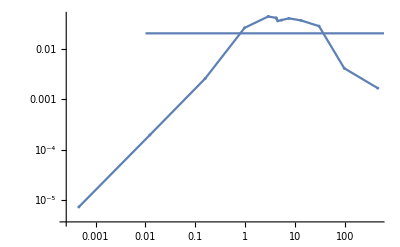

```mathematica
Show[noMkdependencePlot[[1]][[7]],aa]
```

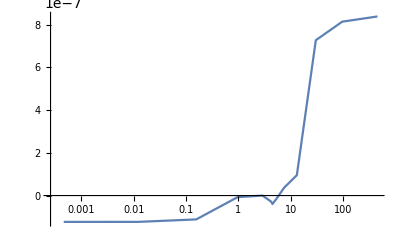
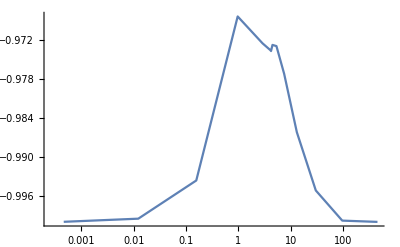
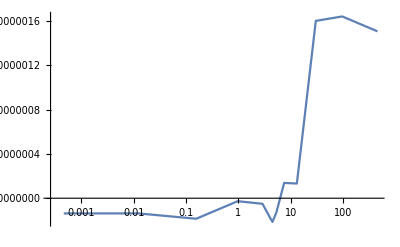
{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}}

Part::partd: Part specification NormConditionMixedPlot⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[NormConditionMixedPlot⟦1⟧,1⟦2⟧,PlotRange→All].

Part::partd: Part specification NormConditionMixedPlot⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[NormConditionMixedPlot⟦1⟧,1⟦2⟧,PlotRange→All].

Part::partd: Part specification NormConditionMixedPlot⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[NormConditionMixedPlot⟦1⟧,1⟦2⟧,PlotRange→All].

Part::partd: Part specification NormConditionMixedPlot⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[NormConditionMixedPlot⟦1⟧,1⟦2⟧,PlotRange→All].

Part::partd: Part specification NormConditionMixedPlot⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[NormConditionMixedPlot⟦1⟧,1⟦2⟧,PlotRange→All].

Part::partd: Part specification NormConditionMixedPlot⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[NormConditionMixedPlot⟦1⟧,1⟦2⟧,PlotRange→All].

```mathematica
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/noMkdependence.mx",noMkdependence];
AlphaMixed = Table[Table[{{noMkdependence[[i]][[n]][[1]],noMkdependence[[i]][[n]][[2]]},{noMkdependence[[i]][[n]][[3]],noMkdependence[[i]][[n]][[4]]}},{n,1,maxN-minN}],{i,1,Length[m1]}];BetaMixed = Table[Table[{{noMkdependence[[i]][[n]][[5]],noMkdependence[[i]][[n]][[6]]},{noMkdependence[[i]][[n]][[7]],noMkdependence[[i]][[n]][[8]]}},{n,1,maxN-minN}],{i,1,Length[m1]}];
NormConditionMixed = Table[Table[AlphaMixed[[i]][[n]].ConjugateTranspose[ AlphaMixed[[i]][[n]]]+Conjugate[BetaMixed[[i]][[n]]].Transpose[BetaMixed[[i]][[n]]],{n,1,maxN-minN}],{i,1,Length[m1]}];
NormConditionMixedPlot = Table[Table[ListLogLinearPlot[Table[{KN[[n]]/f1,Abs[NormConditionMixed[[i]][[n]][[j]][[k]]]-1},{n,1,maxN-minN}], Joined->True, PlotRange->All],{j,1,2},{k,1,2}],{i,1,Length[m1]}]
Manipulate[Show[NormConditionMixedPlot[[i]][[1]][[1]],NormConditionMixedPlot[[i]][[2]][[2]],PlotRange->All],{i,1,Length[m1],1}]
```

## Solve for Bogoliubov coefficients

```mathematica
maxN=200;
minN=-100;
f1=5;
m1={0};
Start=-1;
Stop = -0.01;
NN[n_]:= Piecewise[{{20.82^(1+2.2*(n/maxN)^3), n>=0}, {20.82^(1-3*(-n/minN)^2), n<0}}];
KN=Table[NN[n],{n,minN,maxN}];
```

```mathematica
kdependence = Table[{},{i,1,Length[m1]}];
For[i=1,i<=Length[m1],i++,
kdependence[[i]]=ParallelTable[Evaluate[{a33[η],a34[η],a43[η],a44[η],b33[η],b34[η],b43[η],b44[η]}/.fsolmixed[KN[[n]],m1[[i]],f1,Start,Stop]/.η->Stop][[1]],{n,1,maxN-minN+1},Method->"ItemsPerEvaluation" -> 1];
PrintTemporary[i];
]
DumpSave["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/kdependence.mx",kdependence];
```

```mathematica
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/kdependence.mx",kdependence];
kdependencePlot = Table[Table[ListLogLinearPlot[Table[{KN[[n]]/f1,Abs[kdependence[[i]][[n]][[j]]]},{n,1,maxN-minN}],PlotRange->All,PlotMarkers->{Automatic,3}, Joined->True],{j,1,8}],{i,1,Length[m1]}];
```

```mathematica
Manipulate[kdependencePlot[[i]],{i,1,Length[m1],1}]
```

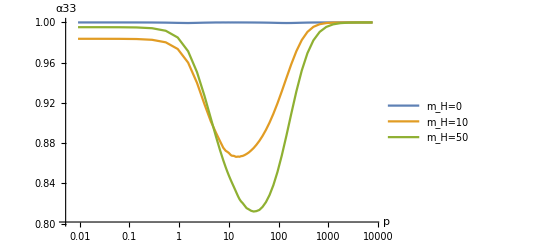
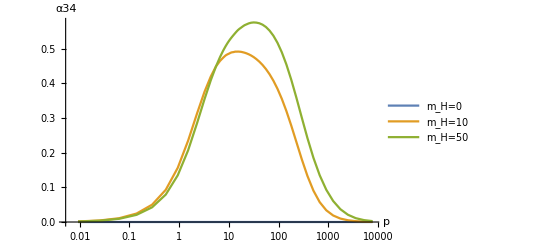
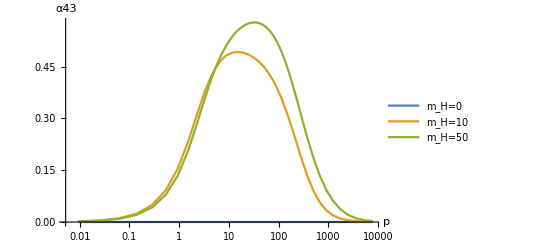
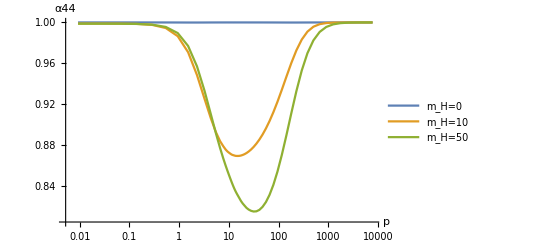
(-Graphics- | -Graphics-
-Graphics- | -Graphics-)

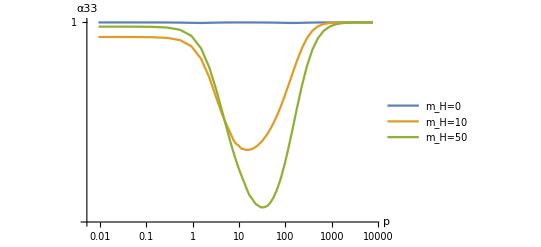
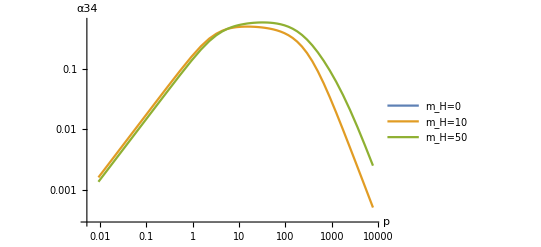
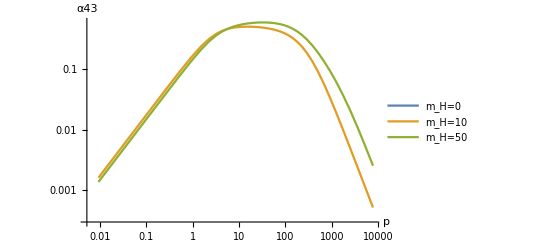
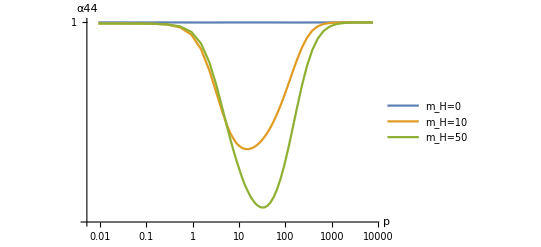
(-Graphics- | -Graphics-
-Graphics- | -Graphics-)

```mathematica
AlphaPlots=Table[ListLogLinearPlot[Table[Table[{KN[[n]],Abs[kdependence[[i]][[n]][[If[j2==1,j1,2+j1]]]]},{n,1,maxN-minN}],{i,1,Length[m1]}], Joined->True,PlotLegends->{"m_H=0","m_H=10","m_H=50"},AxesLabel->{p,ToString[α]<>ToString[2+j1]<>ToString[2+j2]}],{j1,1,2},{j2,1,2}]//MatrixForm
AlphaLogPlots=Table[ListLogLogPlot[Table[Table[{KN[[n]],Abs[kdependence[[i]][[n]][[If[j2==1,j1,2+j1]]]]},{n,1,maxN-minN}],{i,1,Length[m1]}], Joined->True,PlotLegends->{"m_H=0","m_H=10","m_H=50"},AxesLabel->{p,ToString[α]<>ToString[2+j1]<>ToString[2+j2]}],{j1,1,2},{j2,1,2}]//MatrixForm
```

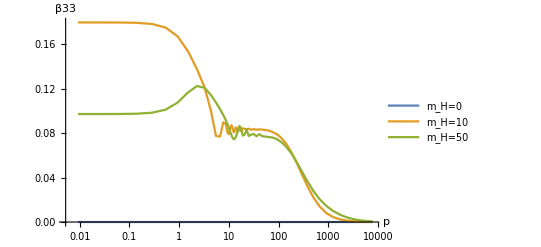
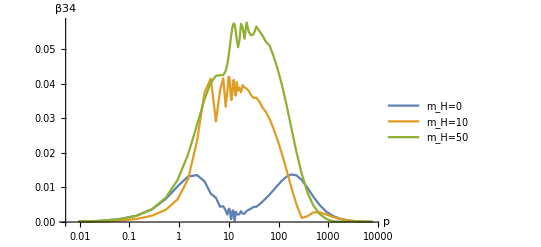
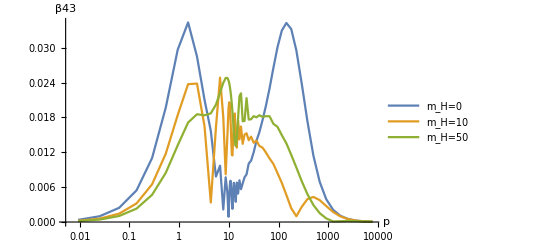
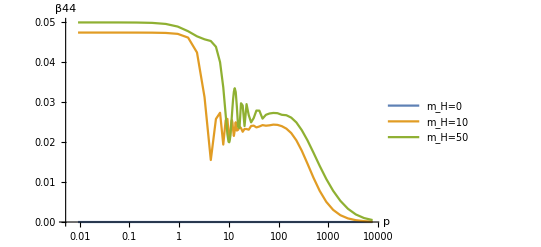
(-Graphics- | -Graphics-
-Graphics- | -Graphics-)

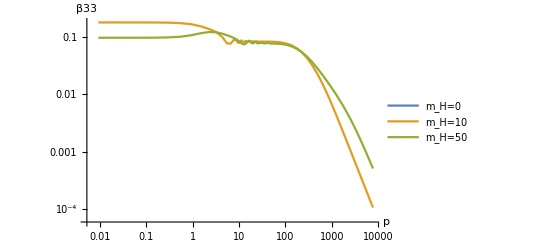
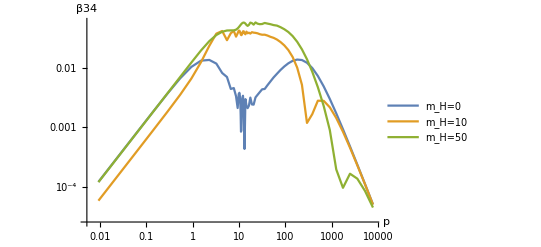
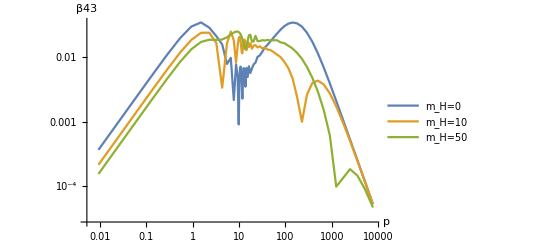
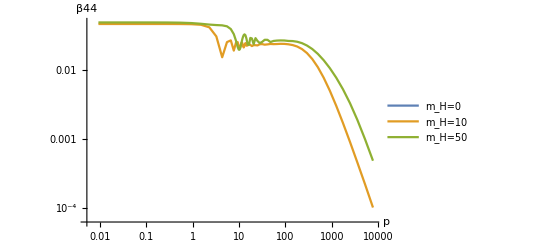
(-Graphics- | -Graphics-
-Graphics- | -Graphics-)

```mathematica
BetaPlots=Table[ListLogLinearPlot[Table[Table[{KN[[n]],Abs[kdependence[[i]][[n]][[If[j2==1,4+j1,6+j1]]]]},{n,1,maxN-minN}],{i,1,Length[m1]}], Joined->True,PlotLegends->{"m_H=0","m_H=10","m_H=50"},AxesLabel->{p,ToString[β]<>ToString[2+j1]<>ToString[2+j2]}],{j1,1,2},{j2,1,2}]//MatrixForm
BetaLogPlots=Table[ListLogLogPlot[Table[Table[{KN[[n]],Abs[kdependence[[i]][[n]][[If[j2==1,4+j1,6+j1]]]]},{n,1,maxN-minN}],{i,1,Length[m1]}], Joined->True,PlotLegends->{"m_H=0","m_H=10","m_H=50"},AxesLabel->{p,ToString[β]<>ToString[2+j1]<>ToString[2+j2]}],{j1,1,2},{j2,1,2}]//MatrixForm
```

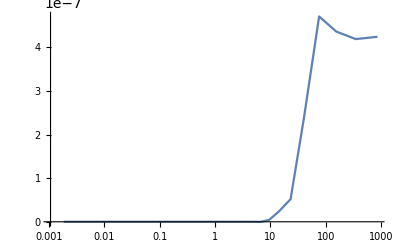
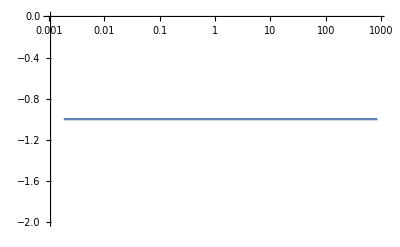
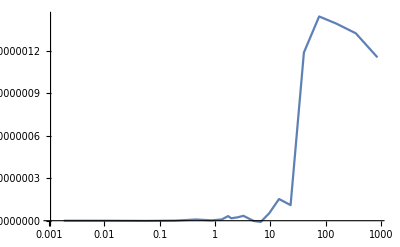
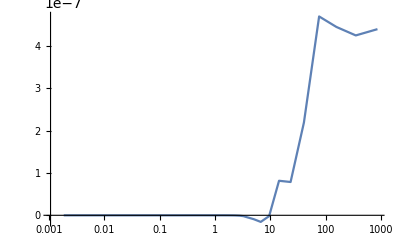
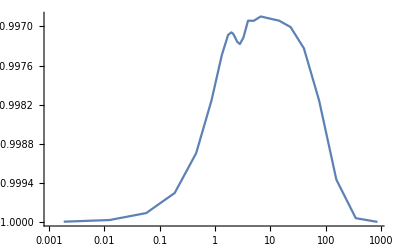
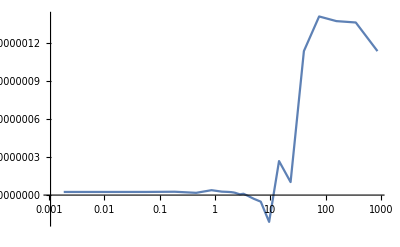
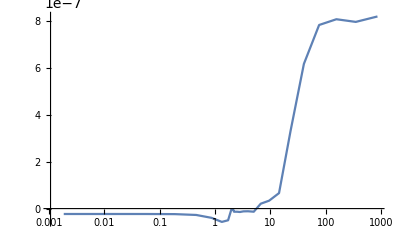
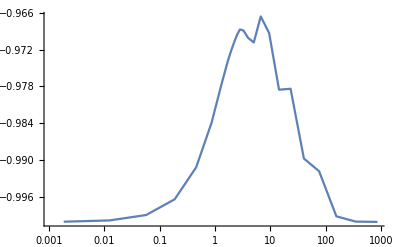
{{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}}

Part::partd: Part specification NormConditionMixedPlot⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[NormConditionMixedPlot⟦1⟧,1⟦2⟧,PlotRange→All].

Part::partd: Part specification NormConditionMixedPlot⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[NormConditionMixedPlot⟦1⟧,1⟦2⟧,PlotRange→All].

Part::partd: Part specification NormConditionMixedPlot⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[NormConditionMixedPlot⟦1⟧,1⟦2⟧,PlotRange→All].

Part::partd: Part specification NormConditionMixedPlot⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[NormConditionMixedPlot⟦1⟧,1⟦2⟧,PlotRange→All].

Part::partd: Part specification NormConditionMixedPlot⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[NormConditionMixedPlot⟦1⟧,1⟦2⟧,PlotRange→All].

Part::partd: Part specification NormConditionMixedPlot⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[NormConditionMixedPlot⟦1⟧,1⟦2⟧,PlotRange→All].

```mathematica
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/kdependence.mx",kdependence];
AlphaMixed = Table[Table[{{kdependence[[i]][[n]][[1]],kdependence[[i]][[n]][[2]]},{kdependence[[i]][[n]][[3]],kdependence[[i]][[n]][[4]]}},{n,1,maxN-minN}],{i,1,Length[m1]}];BetaMixed = Table[Table[{{kdependence[[i]][[n]][[5]],kdependence[[i]][[n]][[6]]},{kdependence[[i]][[n]][[7]],kdependence[[i]][[n]][[8]]}},{n,1,maxN-minN}],{i,1,Length[m1]}];
NormConditionMixed = Table[Table[AlphaMixed[[i]][[n]].ConjugateTranspose[ AlphaMixed[[i]][[n]]]+Conjugate[BetaMixed[[i]][[n]]].Transpose[BetaMixed[[i]][[n]]],{n,1,maxN-minN}],{i,1,Length[m1]}];
NormConditionMixedPlot = Table[Table[ListLogLinearPlot[Table[{KN[[n]],Abs[NormConditionMixed[[i]][[n]][[j]][[k]]]-1},{n,1,maxN-minN}], Joined->True, PlotRange->All],{j,1,2},{k,1,2}],{i,1,Length[m1]}]
Manipulate[Show[NormConditionMixedPlot[[i]][[1]][[1]],NormConditionMixedPlot[[i]][[2]][[2]],PlotRange->All],{i,1,Length[m1],1}]
```

#### Longer evolution

```mathematica
maxN=200;
minN=-100;
f1=5;
m1={0,3,5,10,30,100,300,1000};
Start=-10;
Stop = -0.01;
NN[n_]:= Piecewise[{{20.82^(1+2.2*(n/maxN)^3), n>=0}, {20.82^(1-3*(-n/minN)^2), n<0}}];
KNLong82=Table[NN[n],{n,minN,maxN}];
```

```mathematica
kdependenceLong82 = Table[{},{i,1,Length[m1]}];
For[i=1,i<=Length[m1],i++,
kdependenceLong82[[i]]=ParallelTable[Evaluate[{a33[η],a34[η],a43[η],a44[η],b33[η],b34[η],b43[η],b44[η]}/.fsolmixed[KNLong82[[n]],m1[[i]],f1,Start,Stop]/.η->Stop][[1]],{n,1,maxN-minN+1},Method->"ItemsPerEvaluation" -> 1];
PrintTemporary[i];
]
DumpSave["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/kdependenceLong82.mx",kdependenceLong82];
```

```mathematica
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/kdependenceLong82.mx",kdependenceLong82];
kdependenceLong8Plot = Table[Table[ListLogLinearPlot[Table[{KNLong82[[n]],Abs[kdependenceLong82[[i]][[n]][[j]]]},{n,1,maxN-minN}],PlotRange->All,PlotMarkers->{Automatic,3}, Joined->True],{j,1,8}],{i,1,Length[m1]}];
```

```mathematica
Manipulate[kdependenceLong8Plot[[i]],{i,1,Length[m1],1}]
```

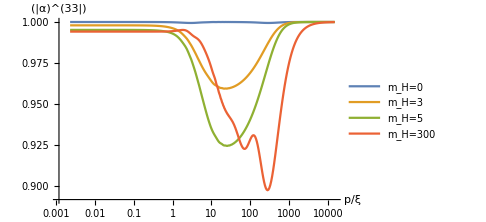
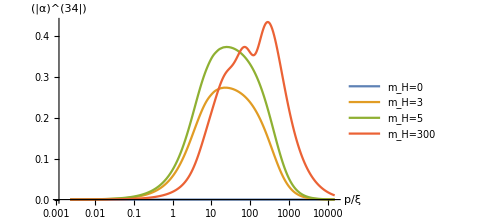
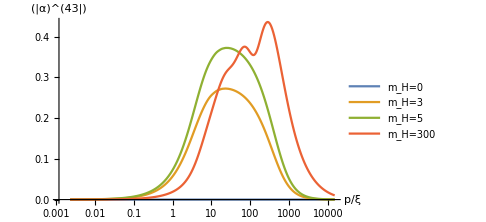
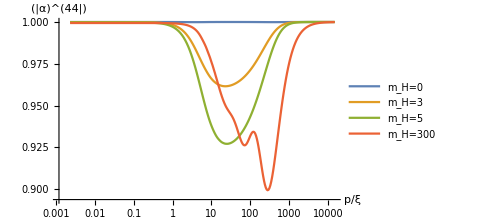
-Graphics- | -Graphics-
-Graphics- | -Graphics-

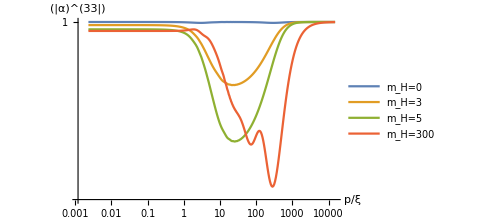
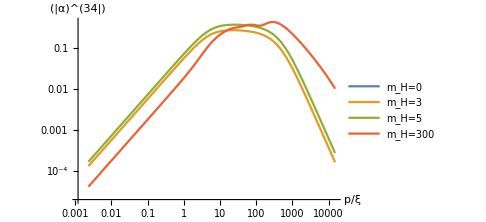
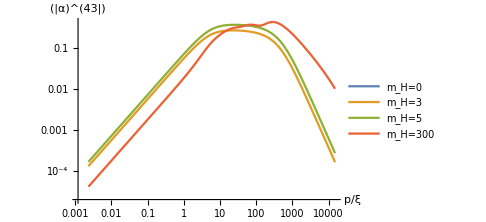
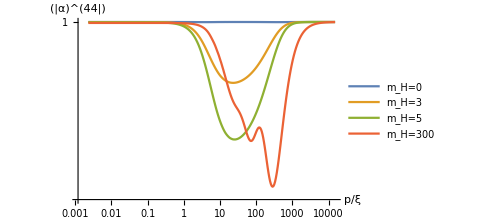
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
AlphaPlots8=Table[ListLogLinearPlot[Table[Table[{KNLong82[[n]],Abs[kdependenceLong82[[i]][[n]][[If[j2==1,j1,2+j1]]]]},{n,1,maxN-minN}],{i,{1,2,3,7}}], Joined->True,PlotLegends->{"m_H=0","m_H=3","m_H=5","m_H=300"},AxesLabel->{p/ξ,"|"<>ToString[α]^ToString[2+j1]<>ToString[2+j2]<>"|"}, ImageSize->Medium],{j1,1,2},{j2,1,2}]//TableForm
AlphaLogPlots8=Table[ListLogLogPlot[Table[Table[{KNLong82[[n]],Abs[kdependenceLong82[[i]][[n]][[If[j2==1,j1,2+j1]]]]},{n,1,maxN-minN}],{i,{1,2,3,7}}], Joined->True,PlotLegends->{"m_H=0","m_H=3","m_H=5","m_H=300"},AxesLabel->{p/ξ,"|"<>ToString[α]^ToString[2+j1]<>ToString[2+j2]<>"|"},ImageSize->Medium],{j1,1,2},{j2,1,2}]//TableForm
```

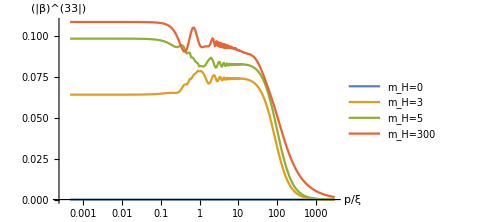
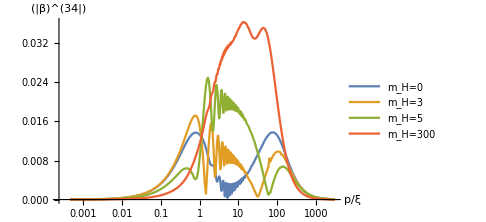
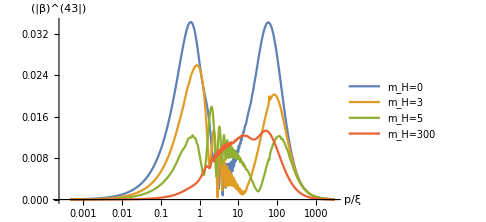
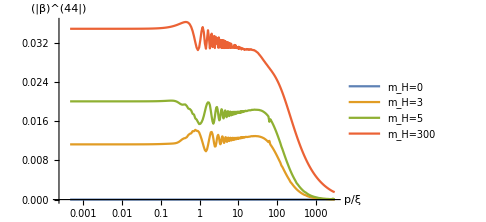
-Graphics- | -Graphics-
-Graphics- | -Graphics-

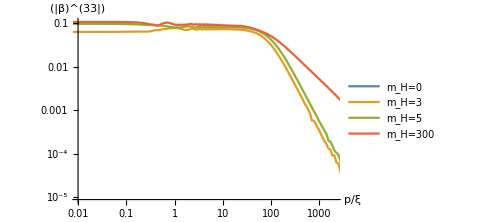
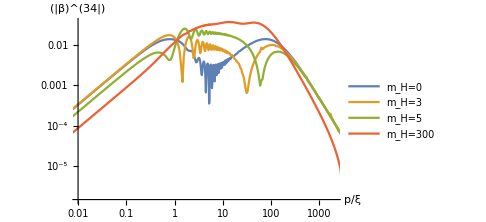
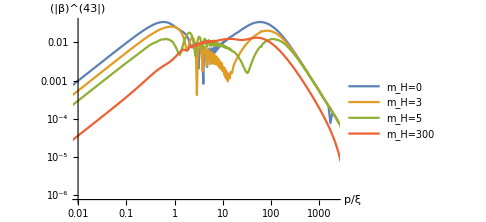
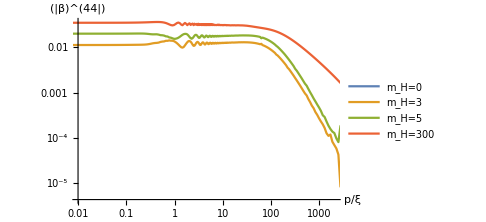
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
BetaPlots8=Table[ListLogLinearPlot[Table[Table[{KNLong82[[n]]/f1,Abs[kdependenceLong82[[i]][[n]][[If[j2==1,j1+4,6+j1]]]]},{n,1,maxN-minN}],{i,{1,2,3,7}}], Joined->True,PlotLegends->{"m_H=0","m_H=3","m_H=5","m_H=300"},AxesLabel->{p/ξ,"|"<>ToString[β]^ToString[2+j1]<>ToString[2+j2]<>"|"}, ImageSize->Medium],{j1,1,2},{j2,1,2}]//TableForm
BetaLogPlots8=Table[ListLogLogPlot[Table[Table[{KNLong82[[n]]/f1,Abs[kdependenceLong82[[i]][[n]][[If[j2==1,j1+4,6+j1]]]]},{n,1,maxN-minN}],{i,{1,2,3,7}}], Joined->True,PlotLegends->{"m_H=0","m_H=3","m_H=5","m_H=300"},AxesLabel->{p/ξ,"|"<>ToString[β]^ToString[2+j1]<>ToString[2+j2]<>"|"},ImageSize->Medium, PlotRange->{{0.01,2100},All}],{j1,1,2},{j2,1,2}]//TableForm
```

```mathematica
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/kdependenceLong82.mx",kdependenceLong82];
AlphaMixed8 = Table[Table[{{kdependenceLong82[[i]][[n]][[1]],kdependenceLong82[[i]][[n]][[2]]},{kdependenceLong82[[i]][[n]][[3]],kdependenceLong82[[i]][[n]][[4]]}},{n,1,maxN-minN}],{i,1,Length[m1]}];BetaMixed8 = Table[Table[{{kdependenceLong82[[i]][[n]][[5]],kdependenceLong82[[i]][[n]][[6]]},{kdependenceLong82[[i]][[n]][[7]],kdependenceLong82[[i]][[n]][[8]]}},{n,1,maxN-minN}],{i,1,Length[m1]}];
NormConditionMixed8 = Table[Table[AlphaMixed8[[i]][[n]].ConjugateTranspose[AlphaMixed8[[i]][[n]]]+Conjugate[BetaMixed8[[i]][[n]]].Transpose[BetaMixed8[[i]][[n]]],{n,1,maxN-minN}],{i,1,Length[m1]}];
NormConditionMixed8Plot = Table[Table[ListLogLinearPlot[Table[{KNLong82[[n]],Abs[NormConditionMixed8[[i]][[n]][[j]][[k]]]-1},{n,1,maxN-minN}], Joined->True, PlotRange->All],{j,1,2},{k,1,2}],{i,1,Length[m1]}];
Manipulate[Show[NormConditionMixed8Plot[[i]][[1]][[1]],NormConditionMixed8Plot[[i]][[2]][[2]],PlotRange->All],{i,1,Length[m1],1}]
```

#### integrate particle production:

```mathematica
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/kdependenceLong82.mx",kdependenceLong82];
IntegratedBetasSquared = Table[{m1[[i]],Table[Sum[Abs[KNLong82[[n]]^2*kdependenceLong82[[i]][[n]][[j]]]^2*(KNLong82[[n+1]]-KNLong82[[n]]),{n,1,maxN-minN}],{j,5,8}]},{i,1,Length[m1]}] //TableForm
```

0 | 0.
2.51884×10^12
2.21608×10^12
0.
3 | 1.04897×10^12
2.41608×10^12
2.18955×10^12
6.60627×10^11
5 | 2.74672×10^12
2.31018×10^12
1.95719×10^12
3.35327×10^12
10 | 1.15669×10^13
2.30811×10^12
1.98749×10^12
7.80286×10^12
30 | 7.57683×10^13
1.53205×10^12
1.43704×10^12
6.01122×10^13
100 | 4.04916×10^14
3.26646×10^11
3.46849×10^11
3.38493×10^14
300 | 7.68606×10^14
2.02964×10^11
2.81153×10^11
7.1222×10^14
1000 | 7.75865×10^14
5.27791×10^11
6.09×10^11
7.18899×10^14

#### Unmixed- DOWN

```mathematica
maxN=300;
minN=-300;
f1=5;
m1={0.1,1,3,10,100};
Start=-10;
Stop = -0.01;
NN[n_]:= Piecewise[{{20.82^(1+2.2*(n/maxN)), n>=0}, {20.82^(1-3*(n/minN)), n<0}}];
KNLong82=Table[NN[n],{n,minN,maxN}];
```

```mathematica
kdependenceDownLong82 = Table[{},{i,1,Length[m1]}];
For[i=1,i<=Length[m1],i++,
kdependenceDownLong82[[i]]=ParallelTable[Evaluate[{a22[η],b22[η]}/.fsoldown[KNLong82[[n]],m1[[i]],f1,Start,Stop]/.η->Stop][[1]],{n,1,maxN-minN+1},Method->"ItemsPerEvaluation" -> 1];
PrintTemporary[i];
]
DumpSave["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/kdependenceDownLong82.mx",kdependenceDownLong82];
```

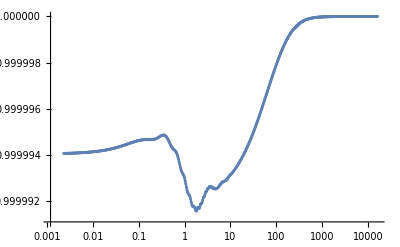
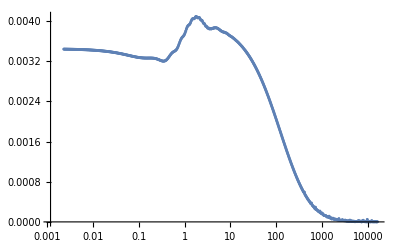
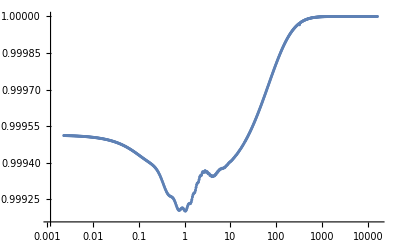
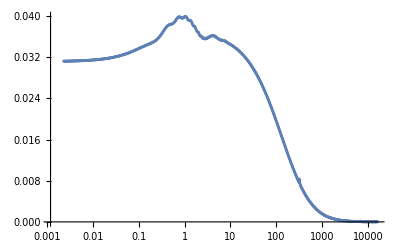
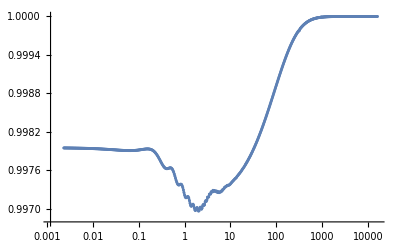
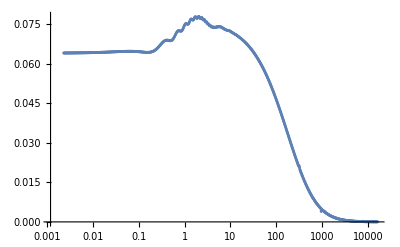
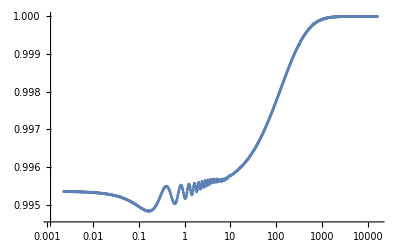
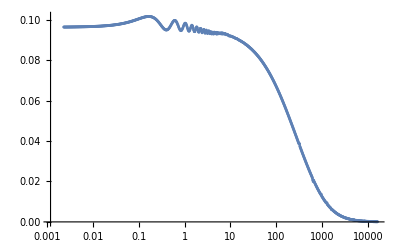

```mathematica
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/kdependenceDownLong82.mx",kdependenceDownLong82];
kdependenceDownLong8Plot = Table[Table[ListLogLinearPlot[Table[{KNLong82[[n]],Abs[kdependenceDownLong82[[i]][[n]][[j]]]},{n,1,maxN-minN}],PlotRange->All,PlotMarkers->{Automatic,3}, Joined->True],{j,1,2}],{i,1,Length[m1]}]
```

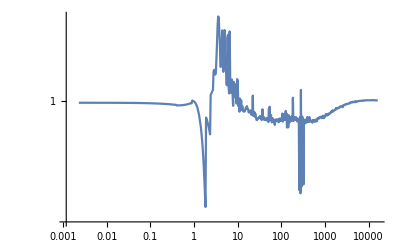
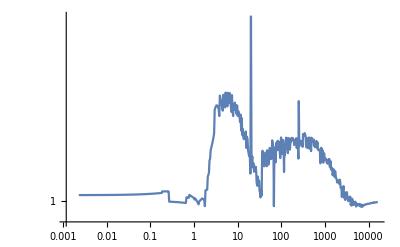
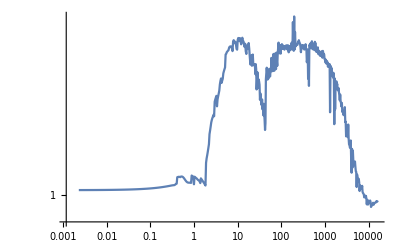
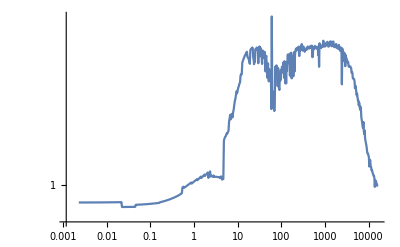
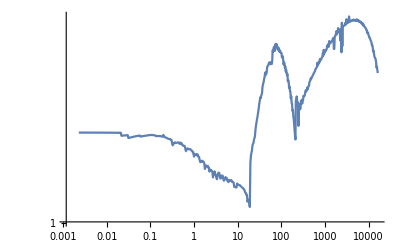

```mathematica
NormConditionDown = Table[Table[Abs[kdependenceDownLong82[[i]][[n]][[1]]]^2+Abs[kdependenceDownLong82[[i]][[n]][[2]]]^2,{n,1,maxN-minN}],{i,1,Length[m1]}];
NormConditionDownPlot = Table[ListLogLogPlot[Table[{KNLong82[[n]],NormConditionDown[[i]][[n]]},{n,1,maxN-minN}], Joined->True, PlotRange->All],{i,1,Length[m1]}]
```

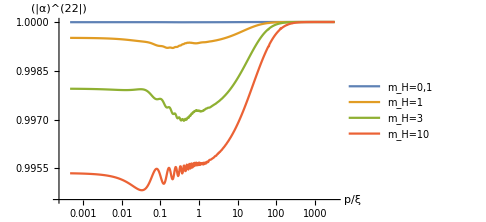

```mathematica
AlphaDownPlots8=ListLogLinearPlot[Table[Table[{KNLong82[[n]]/f1,Abs[kdependenceDownLong82[[i]][[n]][[1]]]},{n,1,maxN-minN}],{i,{1,2,3,4}}], Joined->True,PlotLegends->{"m_H=0,1","m_H=1","m_H=3","m_H=10","m_H=100"},AxesLabel->{p/ξ,"|"<>ToString[α]^ToString[2]<>ToString[2]<>"|"}, ImageSize->Medium]
```

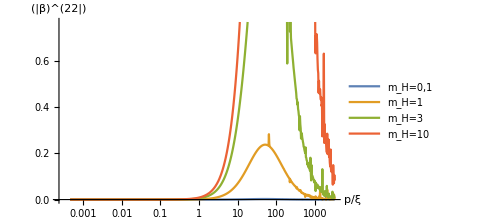

```mathematica
BetaDownPlots8=ListLogLinearPlot[Table[Table[{KNLong82[[n]]/f1,Abs[kdependenceDownLong82[[i]][[n]][[2]]]},{n,1,maxN-minN}],{i,{1,2,3,4}}], Joined->True,PlotLegends->{"m_H=0,1","m_H=1","m_H=3","m_H=10","m_H=100"},AxesLabel->{p/ξ,"|"<>ToString[β]^ToString[2]<>ToString[2]<>"|"}, ImageSize->Medium]
```

```mathematica
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/kdependenceDownLong82.mx",kdependenceDownLong82];
IntegratedBeta22Squared = Table[{m1[[i]],Table[Sum[Abs[KNLong82[[n]]^2*kdependenceDownLong82[[i]][[n]][[j]]]^2*(KNLong82[[n+1]]-KNLong82[[n]]),{n,1,maxN-minN}],{j,2,2}]},{i,1,Length[m1]}] //TableForm
```

0.1 | 1.44948×10^10
1 | 2.34702×10^11
3 | 8.26772×10^11
10 | 8.43529×10^12
100 | 3.65728×10^14

#### Unmixed- UP

```mathematica
maxN=1000;
minN=-600;
f1=5;
m1={0.1,1,3,10,100};
Start=-10;
Stop = -0.01;
NN[n_]:= Piecewise[{{20.82^(1+2.2*(n/maxN)), n>=0}, {20.82^(1-3*(n/minN)), n<0}}];
KNLong82=Table[NN[n],{n,minN,maxN}];
```

```mathematica
kdependenceUpLong82 = Table[{},{i,1,Length[m1]}];
For[i=1,i<=Length[m1],i++,
kdependenceUpLong82[[i]]=ParallelTable[Evaluate[{a11[η],b11[η]}/.fsolup[KNLong82[[n]],m1[[i]],f1,Start,Stop]/.η->Stop][[1]],{n,1,maxN-minN+1},Method->"ItemsPerEvaluation" -> 1];
PrintTemporary[i];
]
DumpSave["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/kdependenceUpLong82.mx",kdependenceUpLong82];
```

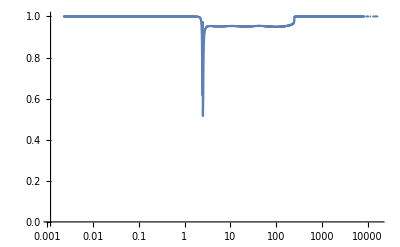
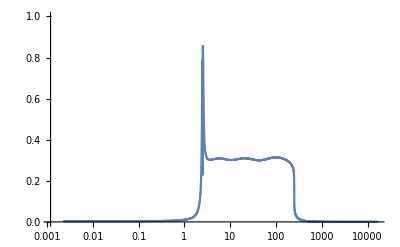
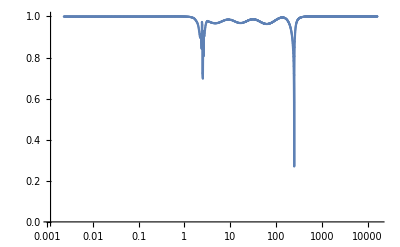
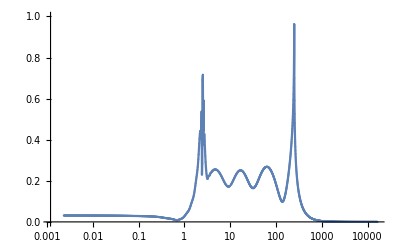
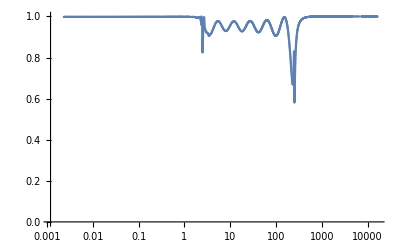
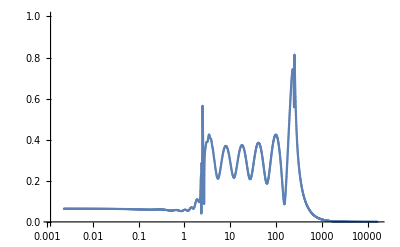
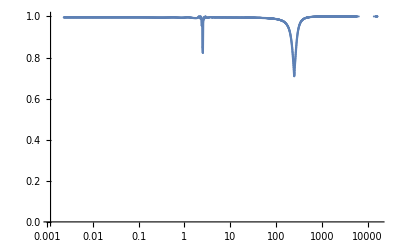
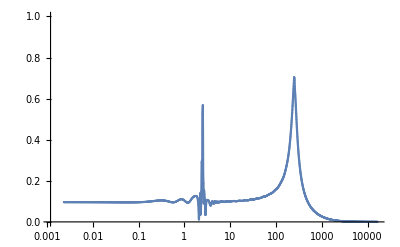

```mathematica
Get["/home/konrad/Documents/Wolfram Mathematica/master_project/correction/kdependenceUpLong82.mx",kdependenceUpLong82];
kdependenceUpLong828Plot = Table[Table[ListLogLinearPlot[Table[{KNLong82[[n]],If[Abs[kdependenceUpLong82[[i]][[n]][[j]]]<1,Abs[kdependenceUpLong82[[i]][[n]][[j]]],Abs[kdependenceUpLong82[[i]][[n-1]][[j]]]<1]},{n,1,maxN-minN}],PlotRange->{0,1},PlotMarkers->{Automatic,2}, Joined->True],{j,1,2}],{i,1,Length[m1]}]
```

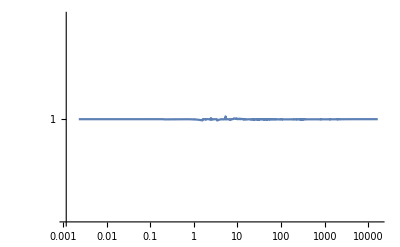
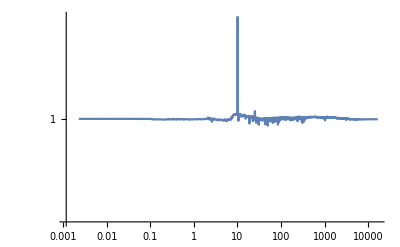
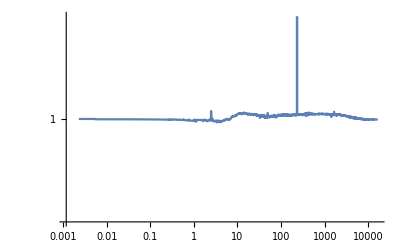
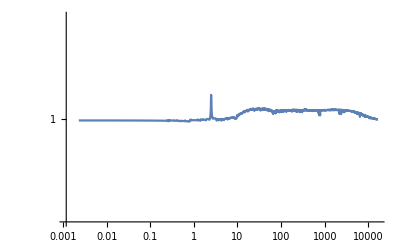
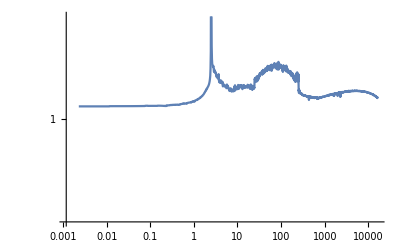

```mathematica
NormConditionUp = Table[Table[Abs[kdependenceUpLong82[[i]][[n]][[1]]]^2+Abs[kdependenceUpLong82[[i]][[n]][[2]]]^2,{n,1,maxN-minN}],{i,1,Length[m1]}];
NormConditionUpPlot = Table[ListLogLogPlot[Table[{KNLong82[[n]],NormConditionUp[[i]][[n]]},{n,1,maxN-minN}], Joined->True, PlotRange->{0.99999,1.00001}],{i,1,Length[m1]}]
```

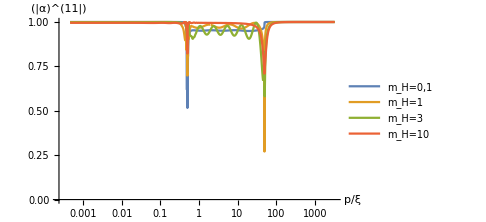

```mathematica
AlphaUpPlots8=ListLogLinearPlot[Table[Table[{KNLong82[[n]]/f1,If[Abs[kdependenceUpLong82[[i]][[n]][[1]]]<50,Abs[kdependenceUpLong82[[i]][[n]][[1]]],Abs[kdependenceUpLong82[[i]][[n-1]][[2]]]<1]},{n,1,maxN-minN}],{i,{1,2,3,4}}], Joined->True,PlotRange->All,PlotLegends->{"m_H=0,1","m_H=1","m_H=3","m_H=10","m_H=100"}, ImageSize->Medium,AxesLabel->{p/ξ,"|"<>ToString[α]^ToString[1]<>ToString[1]<>"|"}]
```

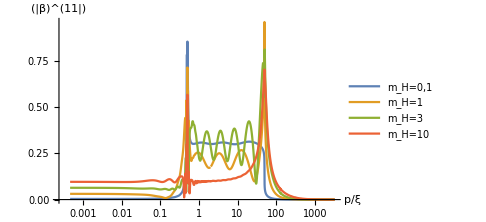

```mathematica
BetaUpPlots8=ListLogLinearPlot[Table[Table[{KNLong82[[n]]/f1,If[Abs[kdependenceUpLong82[[i]][[n]][[2]]]<1,Abs[kdependenceUpLong82[[i]][[n]][[2]]],Abs[kdependenceUpLong82[[i]][[n-1]][[2]]]<1]},{n,1,maxN-minN}],{i,{1,2,3,4}}],PlotRange->All, Joined->True,PlotLegends->{"m_H=0,1","m_H=1","m_H=3","m_H=10","m_H=100"},AxesLabel->{p/ξ,"|"<>ToString[β]^ToString[1]<>ToString[1]<>"|"}, ImageSize->Medium]
```

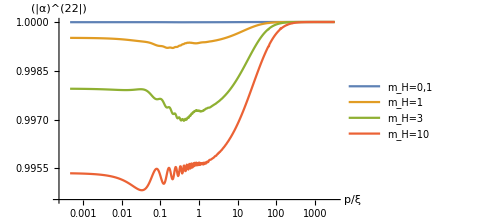
-Graphics- | -Graphics-

```mathematica
Alphas = {{AlphaUpPlots8, AlphaDownPlots8}}//TableForm
```

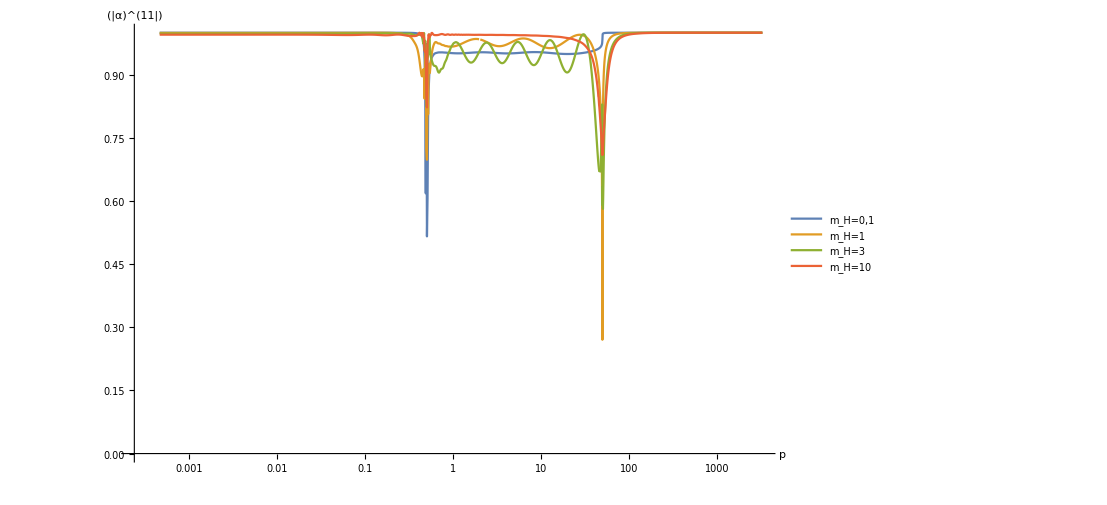
```mathematica
{{-Graphics-_(((_□)_□)_□), -Graphics-}}
```

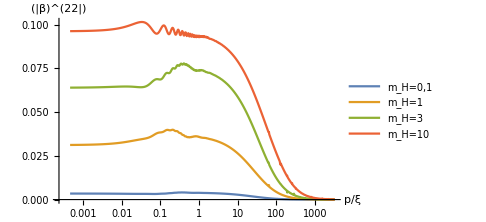
-Graphics- | -Graphics-

```mathematica
Betas = {{BetaUpPlots8, BetaDownPlots8}}//TableForm
```

## Energies

```mathematica
Manipulate[Plot[Evaluate[ωDc[k,f,0.5]],{k,0,170},PlotLabel->t,PlotTheme->NeonColor,PlotRange->Automatic],{f,0,100}]
```

```mathematica
ωDcf[k_,f_,M_]:= {-1/(2f) √((-2 k+f)^2+4 M^2),1/(2f) √((-2 k+f)^2+4 M^2),-1/(2f) √((2 k+f)^2+4 M^2),1/(2f) √((2 k+f)^2+4 M^2),-1/(2f) √(5 f^2+4 (k^2-√(f^2 (k^2+f^2))+M^2)),1/(2f) √(5 f^2+4 (k^2-√(f^2 (k^2+f^2))+M^2)),-1/(2f) √(5 f^2+4 (k^2+√(f^2 (k^2+f^2))+M^2)),1/(2f) √(5 f^2+4 (k^2+√(f^2 (k^2+f^2))+M^2))};
```

```mathematica
ω11[k_,f_,M_]:=ωDcf[k,f,M][[2]];
ω22[k_,f_,M_]:=ωDcf[k,f,M][[4]];
ω33[k_,f_,M_]:=ωDcf[k,f,M][[6]];
ω44[k_,f_,M_]:=ωDcf[k,f,M][[8]];
```

```mathematica
fM={{,},{,},{,}};
```

```mathematica
fM[[1]][[1]]=Plot[{ω11[k,1,0],ω22[k,1,0],ω33[k,1,0],ω44[k,1,0]},{k,-5,5},PlotRange->{0,7},PlotLegends->{"ω_p^1","ω_p^2","ω_p^3","ω_p^4"},AxesLabel->{"p/f","ω_p^j/f(M/f=0)"},ImageSize->Medium];
fM[[1]][[2]]=Plot[{ω11[k,1,1],ω22[k,1,1],ω33[k,1,1],ω44[k,1,1]},{k,-5,5},PlotRange->{0,7},PlotLegends->{"ω_p^1","ω_p^2","ω_p^3","ω_p^4"},AxesLabel->{"p/f","ω_p^j/f(M/f=1)"},ImageSize->Medium];
fM[[2]][[1]]=Plot[{ω11[k,1,2],ω22[k,1,2],ω33[k,1,2],ω44[k,1,2]},{k,-5,5},PlotRange->{0,7},PlotLegends->{"ω_p^1","ω_p^2","ω_p^3","ω_p^4"},AxesLabel->{"p/f","ω_p^j/f(M/f=2)"},ImageSize->Medium];
fM[[2]][[2]]=Plot[{ω11[k,1,4],ω22[k,1,4],ω33[k,1,4],ω44[k,1,4]},{k,-5,5},PlotRange->{0,7},PlotLegends->{"ω_p^1","ω_p^2","ω_p^3","ω_p^4"},AxesLabel->{"p/f","ω_p^j/f(M/f=4)"},ImageSize->Medium];
fM[[3]][[1]]=Plot[{ω11[k,1,5],ω22[k,1,5],ω33[k,1,5],ω44[k,1,5]},{k,0,8},PlotRange->{0,10},PlotLegends->{"ω_p^1","ω_p^2","ω_p^3","ω_p^4"},AxesLabel->{"p/f","ω_p^j/f(M=8)"},ImageSize->Medium];
fM[[3]][[2]]=Plot[{ω11[k,1,5],ω22[k,1,5],ω33[k,1,5],ω44[k,1,5]},{k,0,8},PlotRange->{0,10},PlotLegends->{"ω_p^1","ω_p^2","ω_p^3","ω_p^4"},AxesLabel->{"p/f","ω_p^j/f(M=5)"},ImageSize->Medium];
```

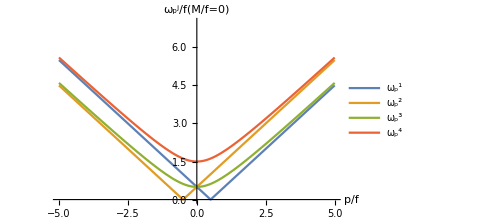
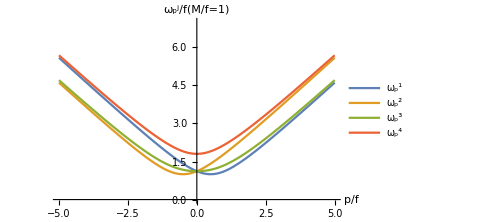
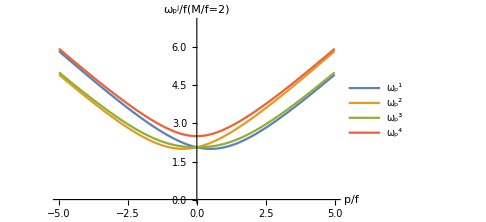
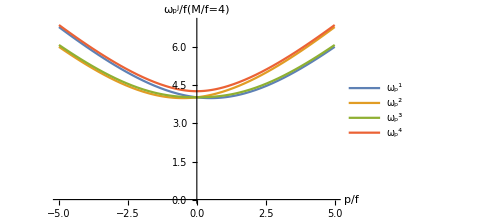
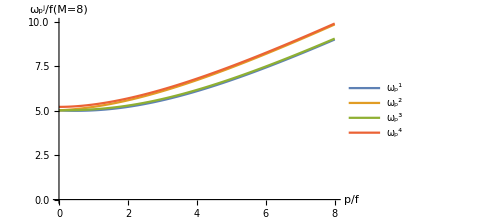
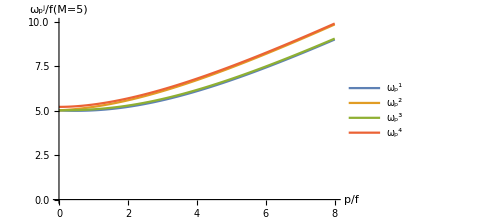
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
fM //TableForm
```

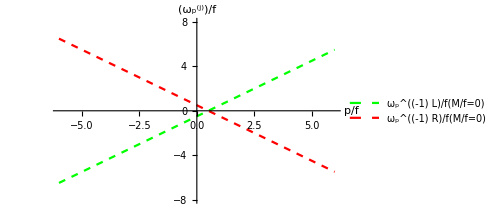

```mathematica
en1plot=Plot[{k-1/2,-k+1/2},{k,-6,6},PlotRange->{-8,8},PlotLegends->{"ω_p^((-1) L)/f(M/f=0)","ω_p^((-1) R)/f(M/f=0)"},AxesLabel->{"p/f","ω_p^(j)/f"},ImageSize->Medium,  PlotStyle->{{Dashed, Green},{Dashed,Red}}]
```

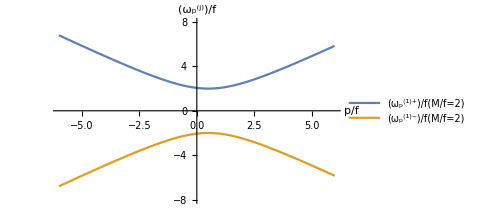

```mathematica
en2plot=Plot[{ω11[k,1,2],-ω11[k,1,2]},{k,-6,6},PlotRange->{-8,8},PlotLegends->{"ω_p^((1)+)/f(M/f=2)","ω_p^((1)-)/f(M/f=2)"},AxesLabel->{"p/f","ω_p^(j)/f"},ImageSize->Medium]
```

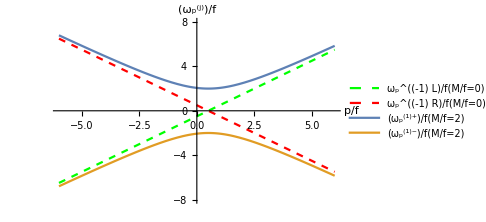

```mathematica
Show[en1plot,en2plot]
```

```mathematica
γ5D = I *γD[[1]].γD[[2]].γD[[3]].γD[[4]];
```

```mathematica
PL = (IdentityMatrix[8]-γ5D)/2;
PR = (IdentityMatrix[8]+γ5D)/2;
```

```mathematica
MM=5;
FF=5;
Dot[nsuD[[6]],PR.nsuD[[6]]]/.ω3->ωDc[k,MM/η,FF/η][[6]]/.M[η]->MM/η/.M[η]^2->(MM/η)^2/.f[η]->FF/η/.f[η]^2->(FF/η)^2/.η->-0.02;
```

```mathematica
PR6[k_]:=Evaluate[Dot[nsuD[[6]],(PR.nsuD[[6]])/Norm[PR.nsuD[[6]]]]/.ω3->ωDc[k,MM/η,FF/η][[6]]/.M[η]->MM/η/.M[η]^2->(MM/η)^2/.f[η]->FF/η/.f[η]^2->(FF/η)^2/.η->-0.02]
PL6[k_]:=Evaluate[Dot[nsuD[[6]],(PL.nsuD[[6]])/Norm[PL.nsuD[[6]]]]/.ω3->ωDc[k,MM/η,FF/η][[6]]/.M[η]->MM/η/.M[η]^2->(MM/η)^2/.f[η]->FF/η/.f[η]^2->(FF/η)^2/.η->-0.02]
PR8[k_]:=Evaluate[Dot[nsuD[[8]],(PR.nsuD[[8]])/Norm[PR.nsuD[[8]]]]/.ω4->ωDc[k,MM/η,FF/η][[8]]/.M[η]->MM/η/.M[η]^2->(MM/η)^2/.f[η]->FF/η/.f[η]^2->(FF/η)^2/.η->-0.02]
PL8[k_]:=Evaluate[Dot[nsuD[[8]],(PL.nsuD[[8]])/Norm[PL.nsuD[[8]]]]/.ω4->ωDc[k,MM/η,FF/η][[8]]/.M[η]->MM/η/.M[η]^2->(MM/η)^2/.f[η]->FF/η/.f[η]^2->(FF/η)^2/.η->-0.02]
```

```mathematica
γ5EigenVectors =(Eigensystem[γ5D][[2]])/(√2);
particles=Table[nsuD[[2*i]],{i,1,4}];
aparticles=Table[nsuD[[2*i-1]],{i,1,4}];
particlesDOTchiral = Table[Dot[γ5EigenVectors[[i]],particles[[j]]],{i,1,8},{j,1,4}];
aparticlesDOTchiral = Table[Dot[γ5EigenVectors[[i]],aparticles[[j]]],{i,1,8},{j,1,4}];
ReplaceRules[k_,η0_,F1_,M1_] := {ω1->ωDc[k,F1/η0,M1/η0][[2]],ω2->ωDc[k,F1/η0,M1/η0][[4]],ω3->ωDc[k,F1/η0,M1/η0][[6]],ω4->ωDc[k,F1/η0,M1/η0][[8]],M[η]->M1/η0,M[η]^2->(M1/η0)^2,f[η]->F1/η0,f[η]^2->(F1/η0)^2};
```

```mathematica
chiralDOTnsuD[k0_,η0_,F1_,M1_]:=Evaluate[Table[Dot[nsuD[[j]],γ5EigenVectors[[i]]],{i,1,8},{j,1,8}]/.ReplaceRules[k,η0,F1,M1]/.k->k0];
```

{A,B^□}=MM {a,b^□}

```mathematica
MM=Table[ArrayFlatten[{{ConjugateTranspose[AlphaMixed8[[i]][[n]]], Transpose[BetaMixed8[[i]][[n]]]},{ConjugateTranspose[BetaMixed8[[i]][[n]]],Transpose[AlphaMixed8[[i]][[n]]]}}],{i,1,3},{n,1,maxN-minN}];
```

Part::partw: Part 301 of … does not exist.

Part::partw: Part 301 of «1» does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
kdependenceLong8 = kdependenceLong82;
```

```mathematica
maxN=200;
minN=-100;
NN[n_]:= Piecewise[{{20.82^(1+2.2*(n/maxN)^3), n>=0}, {20.82^(1-3*(-n/minN)^2), n<0}}];
KN=Table[NN[n],{n,minN,maxN}];
```

```mathematica
BetaRight[j_] :=Parallelize[Table[1/(√2)Evaluate[√(
(Abs[kdependenceLong8[[j]][[n]][[6]]]^2+Abs[kdependenceLong8[[j]][[n]][[8]]]^2)*Sum[Abs[chiralDOTnsuD[k0,η,5,M1][[i]][[7]]]^2+Abs[chiralDOTnsuD[k0,η,5,M1][[i]][[8]]]^2,{i,1,4}]+  (Abs[kdependenceLong8[[j]][[n]][[7]]]^2+Abs[kdependenceLong8[[j]][[n]][[5]]]^2)*Sum[Abs[chiralDOTnsuD[k0,η,5,M1][[i]][[5]]]^2+Abs[chiralDOTnsuD[k0,η,5,M1][[i]][[6]]]^2,{i,1,4}]
)/.k0->NN[n+minN -1]//.M1->m1[[j]]/.η->-0.02],{n,1,maxN-minN}]]
BetaLeft[j_] :=Parallelize[Table[1/(√2)Evaluate[√(
  ( Abs[kdependenceLong8[[j]][[n]][[6]]]^2+Abs[kdependenceLong8[[j]][[n]][[8]]]^2)*Sum[Abs[chiralDOTnsuD[k0,η,5,M1][[i]][[7]]]^2+Abs[chiralDOTnsuD[k0,η,5,M1][[i]][[8]]]^2,{i,5,8}]+  (Abs[kdependenceLong8[[j]][[n]][[7]]]^2+Abs[kdependenceLong8[[j]][[n]][[5]]]^2)*Sum[Abs[chiralDOTnsuD[k0,η,5,M1][[i]][[5]]]^2+Abs[chiralDOTnsuD[k0,η,5,M1][[i]][[6]]]^2,{i,5,8}]
)/.k0->NN[n+minN -1]//.M1->m1[[j]]/.η->-0.02],{n,1,maxN-minN}]]
```

```mathematica
BetaRights = Table[BetaRight[i],{i,1,Length[m1]}];
BetaLefts = Table[BetaLeft[i],{i,1,Length[m1]}];
```

```mathematica
BetaDifferences = Table[BetaRights[[i]][[n]]-BetaLefts[[i]][[n]],{i,1,Length[m1]},{n,1,maxN-minN}];
```

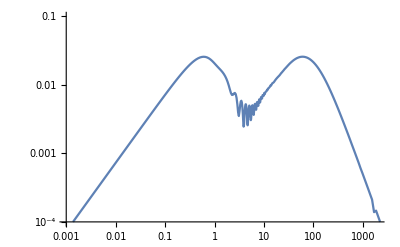
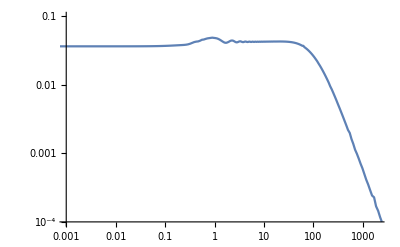
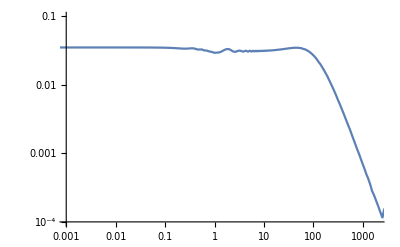
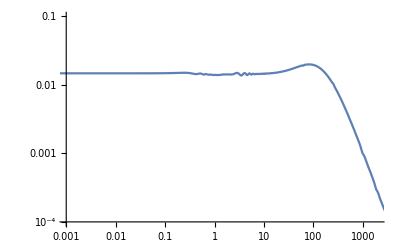
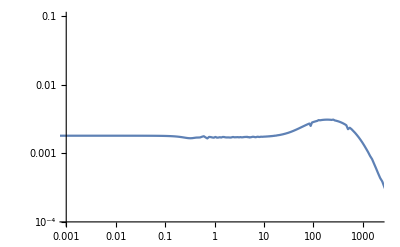

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
BeteRightPlots=Table[ListLogLogPlot[Table[{KN[[n]]/f1,BetaRights[[i]][[n]]},{n,1,maxN-minN}],PlotRange->{{0.001,2000},{0.0001,0.1}},Joined->True],{i,1,Length[m1]}]
BeteLeftPlots = Table[ListLogLogPlot[Table[{KN[[n]]/f1,BetaLefts[[i]][[n]]},{n,1,maxN-minN}],PlotRange->{{0.001,2000},{0.0001,0.1}},Joined->True],{i,1,Length[m1]}]
```

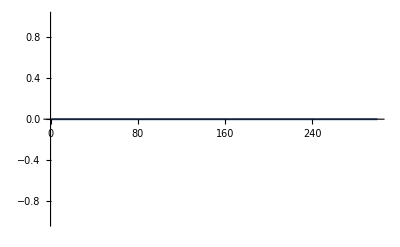
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
BeteDiffPlots =Table[ListPlot[Table[BetaDifferences[[i]][[n]],{n,1,maxN-minN}],Joined->True],{i,1,Length[m1]}]
```

```mathematica
aa=LogLogPlot[0.02,{x,0.01,1000}];
```

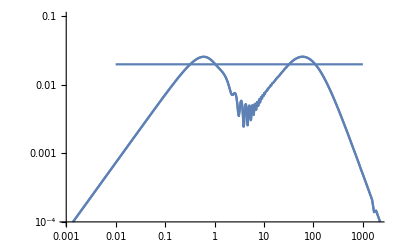

```mathematica
Table[Show[BeteRightPlots[[i]],BeteLeftPlots[[i]],aa],{i,1,1}]
```

```mathematica
valeriesPlotData = Import["/home/konrad/Downloads/data_valeries_plot.csv"];
```

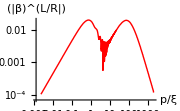

```mathematica
valeriesPlot=ListLogLogPlot[valeriesPlotData, Joined->True, PlotStyle->{Red,Thin},AxesLabel->{p/ξ,"|"<>ToString[β]^ToString[L]<>ToString["/"]<>ToString[R]<>"|"}, ImageSize->Small]
```

```mathematica
Manipulate[Show[ListLogLogPlot[Table[{KN[[n]]/f1*x,BetaRights[[1]][[n]]*y},{n,1,maxN-minN}],PlotRange->{{0.001,2000},{0.0001,0.1}},Joined->True,AxesLabel->{p/ξ,Abs[Subscript[ToString[β],ToString["R\L"]]]}],valeriesPlot],{x,0.8,1.2},{y,0.7,1.01}]
```

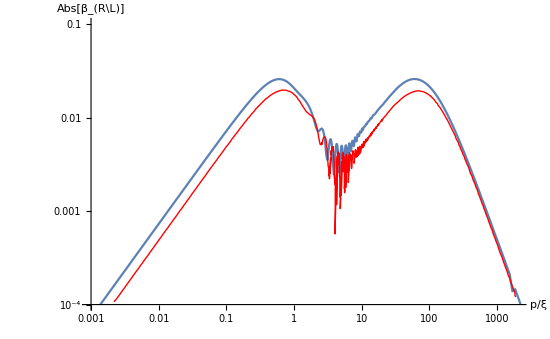

```mathematica
Show[ListLogLogPlot[Table[{KN[[n]]/f1,BetaRights[[1]][[n]]},{n,1,maxN-minN}],PlotRange->{{0.001,2000},{0.0001,0.1}},Joined->True,AxesLabel->{p/ξ,Abs[Subscript[ToString[β],ToString["R\L"]]]}],valeriesPlot]
```

```mathematica
0.7515
N[1/(√2)]
```

0.7515

0.707107